# GCascade Notebook

## Importing and Setting up the Package

```mathematica
AppendTo[$Path, NotebookDirectory[]];
```

```mathematica
<<GCascadeV3.wl
```

You Have Imported GCascade. Setup will take about a minute.

## Getting Flux Functions for Gamma Rays

```mathematica
Get["/Users/barbaraskrzypek/Documents/IceCube/GCascade-master/EGgammaFluxDec.m"];
```

## Plot Formatting

```mathematica
ticks={{Flatten[{Table[{10^x,("10")^ToString[x]},{x,-100,100}],Flatten[Table[{y*10^x,""},{y,2,9},{x,-100,100}],1]},1],None},
{Flatten[{{{0.1 ,"10^-1"}},{{1 ,"1"}},Table[{10^x,("10")^ToString[x]},{x,1,12,1}],Flatten[Table[{y*10^x,""},{y,2,9},{x,-100,100}],1]},1]
,None}};
```

## Propagating Gamma Rays

Injected Spectrum

## Cutoff Power Law

```mathematica
injSpectrum = Table[cutoffPowerLaw[energies[[i]],2.0,10^13, 3.12*10^42],{i,1,Length[energies]}];
```

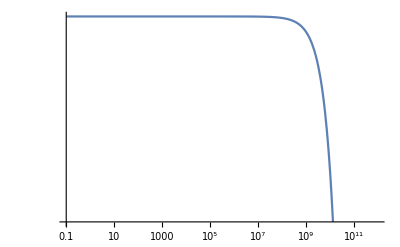

```mathematica
injectedPlot = specPlot[injSpectrum]
```

## BB Decay Mode

### mDM = 10 GeV (doesn’t work)

```mathematica
injSpectrumBB10 = Table[10^(energies[[i]]*EGgammaFluxDec["b","noUV"][10,10^-26,Log[10,energies[[i]]]]),{i,1,Length[energies]}]
```

{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
pBB10=LogLogPlot[Interpolation[Thread[{energies,energies^2 injSpectrumBB10}]][x],{x,10^0,10^2},
PlotRange->{{10^0,10^2},{10^-7,10^-5}},
PlotStyle->{Red,Thick},
FrameTicks->ticks
];
```

```mathematica
Show[pBB10,
Axes->False,
Frame->True,
FrameStyle-> Thickness[0.004],
FrameTicksStyle-> Thickness[0.004],
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
LabelStyle-> Directive[Bold,Black,FontFamily-> "Helvetica",FontSize-> 14],
ImageSize->Large
]
```

-Graphics-

```mathematica
specPlot[injSpectrumBB10]
```

-Graphics-

### mDM = 100 GeV

```mathematica
injSpectrumBB100 = Table[10^(1/energies[[i]] EGgammaFluxDec["b","noUV"][100,10^-26,Log[10,energies[[i]]]]),{i,1,Length[energies]}];
```

```mathematica
pB100=LogLogPlot[Interpolation[Thread[{energies,energies^2 injSpectrumBB100}]][x],{x,10^-3,10^5},
PlotRange->{{10^-3,10^5},{10^-1,10^4}},
PlotStyle->{Red,Thick},
FrameTicks->ticks
];
```

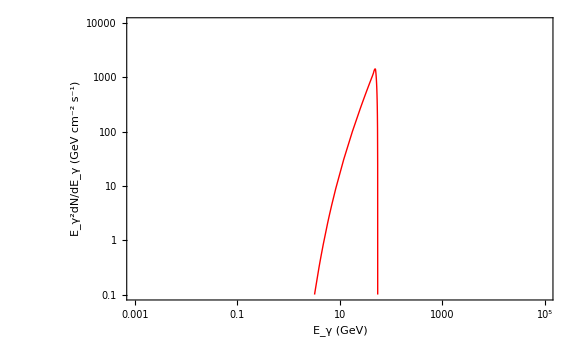

```mathematica
Show[pB100,
Axes->False,
Frame->True,
FrameStyle-> Thickness[0.004],
FrameTicksStyle-> Thickness[0.004],
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
LabelStyle-> Directive[Bold,Black,FontFamily-> "Helvetica",FontSize-> 14],
ImageSize->Large
]
```

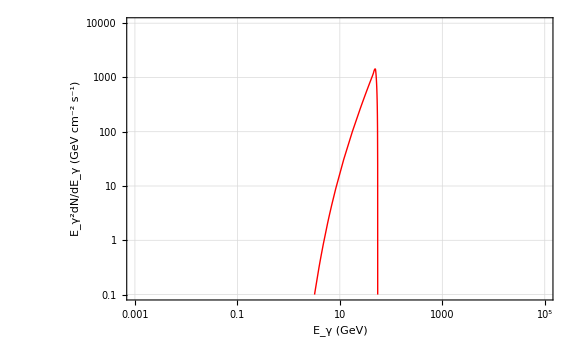

```mathematica
Module[{A,f1,f2,m1,envstyle,minE,maxE,expTicks},
A=2;
m1=81;
f1[x_]:=4/5. fVVqq[x]+1/5. fVVbb[x];
f2=fVVqq;
envstyle={(*Thick,*)Thickness[.01],Opacity[.3,Gray]};
minE=.75;
maxE=30;
expTicks=Table[{10^i,exponentForm[10^i]},{i,-8,-6}];
Show[pB100,PlotStyle->{
envstyle,
envstyle,
{Thickness[.008],Blue}
},
Filling->{1->{2}},
FillingStyle->{Opacity[.2,Yellow]},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
ImageSize->Large, (* or Large*)
Epilog->{
Text[Rotate[Style["m_χ→ bb",20,Gray],0Degree],ImageScaled@{.25,.85}],
Text[Rotate[Style["m_χ = 100 GeV",20,Gray],0Degree],ImageScaled@{.25,.75}]
(*Text[Rotate[Style["bb",19,Blue],0Degree],ImageScaled@{.27,.92}],
Text[Rotate[Style["m_χ=40 GeV",17,Blue],0Degree],ImageScaled@{.27,.78}],
Text[Rotate[Style["VV (V→qq)",19,Red],0Degree],ImageScaled@{.83,.84}],
Text[Rotate[Style["m_χ=81, m_V=21 GeV",17,Red],0Degree],ImageScaled@{.82,.76}],
Text[Rotate[Style["3φ (φ→bb)",19,Darker[Green]],0Degree],ImageScaled@{.5,.55}],
Text[Rotate[Style["m_χ=123, m_φ=27 GeV",17,Darker[Green]],0Degree],ImageScaled@{.5,.45}],
Text[Style["a=2",19,Gray],ImageScaled@{.2,.23}]*)
}
(*PlotLegends->Placed[LineLegend[Range[1,6],LegendLayout->{"Row",2}],{.35,.25}]*)
(*PlotTheme->"Detailed"*)
]]
```

### mDM = 1 TeV

```mathematica
injSpectrumBB1000 = Table[10^(1/energies[[i]] EGgammaFluxDec["b","noUV"][1000,10^-26,Log[10,energies[[i]]]]),{i,1,Length[energies]}];
```

```mathematica
pB1000=LogLogPlot[Interpolation[Thread[{energies,energies^2 injSpectrumBB1000}]][x],{x,10^-1,10^4},
PlotRange->{{10^-1,10^4},{10^2,10^6}},
PlotStyle->{Red,Thick},
FrameTicks->ticks
];
```

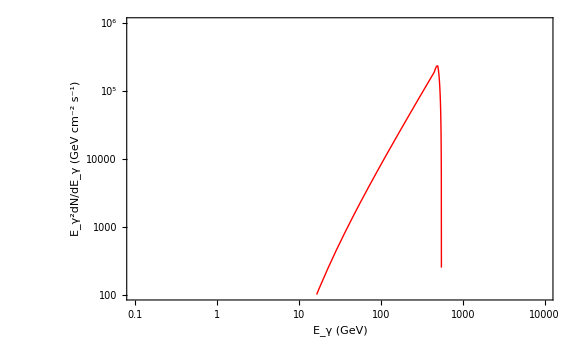

```mathematica
Show[pB1000,
Axes->False,
Frame->True,
FrameStyle-> Thickness[0.004],
FrameTicksStyle-> Thickness[0.004],
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
LabelStyle-> Directive[Bold,Black,FontFamily-> "Helvetica",FontSize-> 14],
ImageSize->Large
]
```

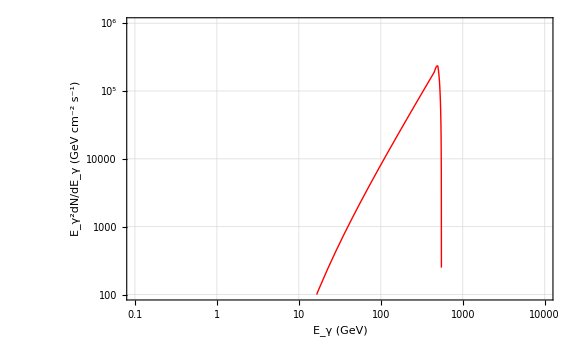

```mathematica
Module[{A,f1,f2,m1,envstyle,minE,maxE,expTicks},
A=2;
m1=81;
f1[x_]:=4/5. fVVqq[x]+1/5. fVVbb[x];
f2=fVVqq;
envstyle={(*Thick,*)Thickness[.01],Opacity[.3,Gray]};
minE=.75;
maxE=30;
expTicks=Table[{10^i,exponentForm[10^i]},{i,-8,-6}];
Show[pB1000,PlotStyle->{
envstyle,
envstyle,
{Thickness[.008],Blue}
},
Filling->{1->{2}},
FillingStyle->{Opacity[.2,Yellow]},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
ImageSize->Large, (* or Large*)
Epilog->{
Text[Rotate[Style["m_χ→ bb",20,Gray],0Degree],ImageScaled@{.25,.85}],
Text[Rotate[Style["m_χ = 1 TeV",20,Gray],0Degree],ImageScaled@{.25,.75}]
(*Text[Rotate[Style["bb",19,Blue],0Degree],ImageScaled@{.27,.92}],
Text[Rotate[Style["m_χ=40 GeV",17,Blue],0Degree],ImageScaled@{.27,.78}],
Text[Rotate[Style["VV (V→qq)",19,Red],0Degree],ImageScaled@{.83,.84}],
Text[Rotate[Style["m_χ=81, m_V=21 GeV",17,Red],0Degree],ImageScaled@{.82,.76}],
Text[Rotate[Style["3φ (φ→bb)",19,Darker[Green]],0Degree],ImageScaled@{.5,.55}],
Text[Rotate[Style["m_χ=123, m_φ=27 GeV",17,Darker[Green]],0Degree],ImageScaled@{.5,.45}],
Text[Style["a=2",19,Gray],ImageScaled@{.2,.23}]*)
}
(*PlotLegends->Placed[LineLegend[Range[1,6],LegendLayout->{"Row",2}],{.35,.25}]*)
(*PlotTheme->"Detailed"*)
]]
```

### mDM = 10 TeV

```mathematica
injSpectrumBB10000 = Table[10^(1/energies[[i]] EGgammaFluxDec["b","noUV"][10000,10^-26,Log[10,energies[[i]]]]),{i,1,Length[energies]}];
```

```mathematica
pB10000=LogLogPlot[Interpolation[Thread[{energies,energies^2 injSpectrumBB10000}]][x],{x,10^-3,10^5},
PlotRange->{{10^-3,10^5},{10^3,10^8}},
PlotStyle->{Red,Thick},
FrameTicks->ticks
];
```

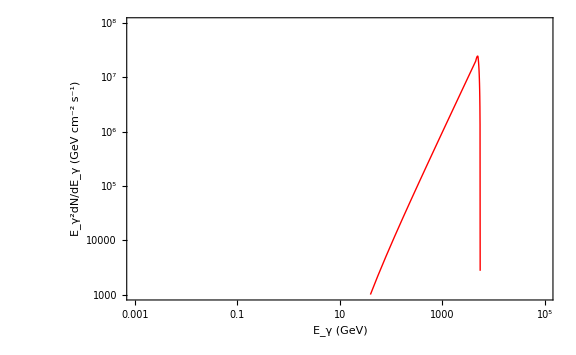

```mathematica
Show[pB10000,
Axes->False,
Frame->True,
FrameStyle-> Thickness[0.004],
FrameTicksStyle-> Thickness[0.004],
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
LabelStyle-> Directive[Bold,Black,FontFamily-> "Helvetica",FontSize-> 14],
ImageSize->Large
]
```

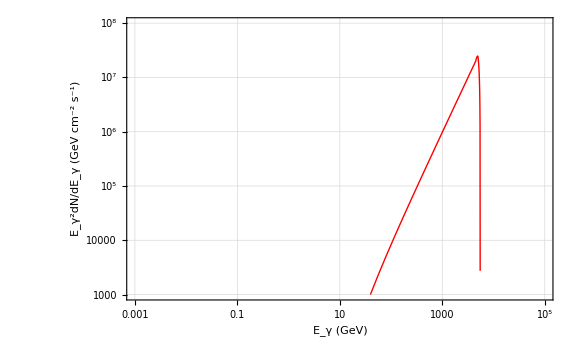

```mathematica
Module[{A,f1,f2,m1,envstyle,minE,maxE,expTicks},
A=2;
m1=81;
f1[x_]:=4/5. fVVqq[x]+1/5. fVVbb[x];
f2=fVVqq;
envstyle={(*Thick,*)Thickness[.01],Opacity[.3,Gray]};
minE=.75;
maxE=30;
expTicks=Table[{10^i,exponentForm[10^i]},{i,-8,-6}];
Show[pB10000,PlotStyle->{
envstyle,
envstyle,
{Thickness[.008],Blue}
},
Filling->{1->{2}},
FillingStyle->{Opacity[.2,Yellow]},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
ImageSize->Large, (* or Large*)
Epilog->{
Text[Rotate[Style["m_χ→ bb",20,Gray],0Degree],ImageScaled@{.25,.85}],
Text[Rotate[Style["m_χ = 10 TeV",20,Gray],0Degree],ImageScaled@{.25,.75}]
(*Text[Rotate[Style["bb",19,Blue],0Degree],ImageScaled@{.27,.92}],
Text[Rotate[Style["m_χ=40 GeV",17,Blue],0Degree],ImageScaled@{.27,.78}],
Text[Rotate[Style["VV (V→qq)",19,Red],0Degree],ImageScaled@{.83,.84}],
Text[Rotate[Style["m_χ=81, m_V=21 GeV",17,Red],0Degree],ImageScaled@{.82,.76}],
Text[Rotate[Style["3φ (φ→bb)",19,Darker[Green]],0Degree],ImageScaled@{.5,.55}],
Text[Rotate[Style["m_χ=123, m_φ=27 GeV",17,Darker[Green]],0Degree],ImageScaled@{.5,.45}],
Text[Style["a=2",19,Gray],ImageScaled@{.2,.23}]*)
}
(*PlotLegends->Placed[LineLegend[Range[1,6],LegendLayout->{"Row",2}],{.35,.25}]*)
(*PlotTheme->"Detailed"*)
]]
```

### mDM = 100 TeV

```mathematica
injSpectrumBB100000 = Table[10^(1/energies[[i]] EGgammaFluxDec["b","noUV"][100000,10^-26,Log[10,energies[[i]]]]),{i,1,Length[energies]}];
```

```mathematica
pB100000=LogLogPlot[Interpolation[Thread[{energies,energies^2 injSpectrumBB100000}]][x],{x,10^2,10^6},
PlotRange->{{10^2,10^6},{10^6,10^10}},
PlotStyle->{Red,Thick},
FrameTicks->ticks
];
```

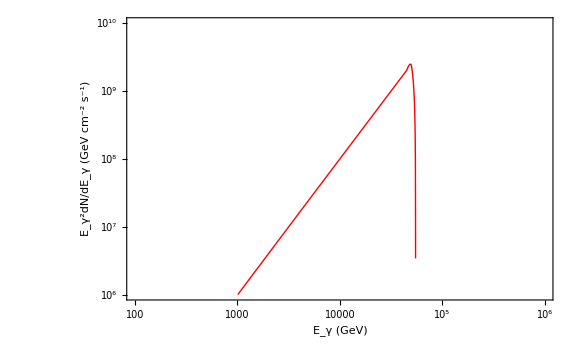

```mathematica
Show[pB100000,
Axes->False,
Frame->True,
FrameStyle-> Thickness[0.004],
FrameTicksStyle-> Thickness[0.004],
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
LabelStyle-> Directive[Bold,Black,FontFamily-> "Helvetica",FontSize-> 14],
ImageSize->Large
]
```

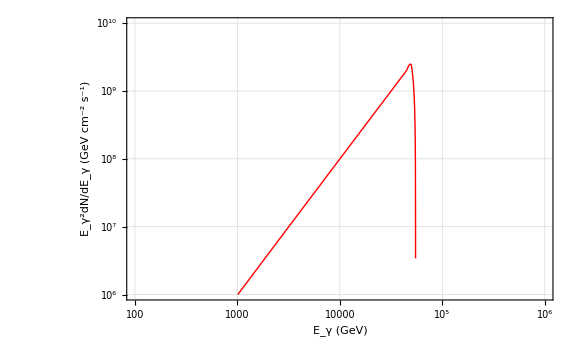

```mathematica
Module[{A,f1,f2,m1,envstyle,minE,maxE,expTicks},
A=2;
m1=81;
f1[x_]:=4/5. fVVqq[x]+1/5. fVVbb[x];
f2=fVVqq;
envstyle={(*Thick,*)Thickness[.01],Opacity[.3,Gray]};
minE=.75;
maxE=30;
expTicks=Table[{10^i,exponentForm[10^i]},{i,-8,-6}];
Show[pB100000,PlotStyle->{
envstyle,
envstyle,
{Thickness[.008],Blue}
},
Filling->{1->{2}},
FillingStyle->{Opacity[.2,Yellow]},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
ImageSize->Large, (* or Large*)
Epilog->{
Text[Rotate[Style["m_χ→ bb",20,Gray],0Degree],ImageScaled@{.25,.85}],
Text[Rotate[Style["m_χ = 100 TeV",20,Gray],0Degree],ImageScaled@{.25,.75}]
(*Text[Rotate[Style["bb",19,Blue],0Degree],ImageScaled@{.27,.92}],
Text[Rotate[Style["m_χ=40 GeV",17,Blue],0Degree],ImageScaled@{.27,.78}],
Text[Rotate[Style["VV (V→qq)",19,Red],0Degree],ImageScaled@{.83,.84}],
Text[Rotate[Style["m_χ=81, m_V=21 GeV",17,Red],0Degree],ImageScaled@{.82,.76}],
Text[Rotate[Style["3φ (φ→bb)",19,Darker[Green]],0Degree],ImageScaled@{.5,.55}],
Text[Rotate[Style["m_χ=123, m_φ=27 GeV",17,Darker[Green]],0Degree],ImageScaled@{.5,.45}],
Text[Style["a=2",19,Gray],ImageScaled@{.2,.23}]*)
}
(*PlotLegends->Placed[LineLegend[Range[1,6],LegendLayout->{"Row",2}],{.35,.25}]*)
(*PlotTheme->"Detailed"*)
]]
```

## WW Decay Mode

### mDM = 1 TeV

```mathematica
injSpectrumWW1000 = Table[10^(1/energies[[i]] EGgammaFluxDec["W","noUV"][1000,10^-26,Log[10,energies[[i]]]]),{i,1,Length[energies]}];
```

```mathematica
pW1000=LogLogPlot[Interpolation[Thread[{energies,energies^2 injSpectrumWW1000}]][x],{x,10^-1,10^6},
PlotRange->{{10^-1,10^6},{10^-3,10^10}},
PlotStyle->{Blue,Thick},
FrameTicks->ticks
];
```

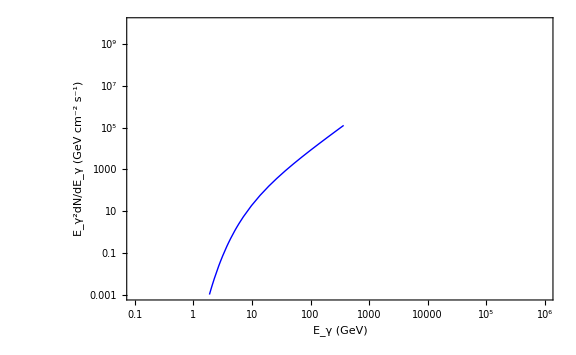

```mathematica
Show[pW1000,
Axes->False,
Frame->True,
FrameStyle-> Thickness[0.004],
FrameTicksStyle-> Thickness[0.004],
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
LabelStyle-> Directive[Bold,Black,FontFamily-> "Helvetica",FontSize-> 14],
ImageSize->Large
]
```

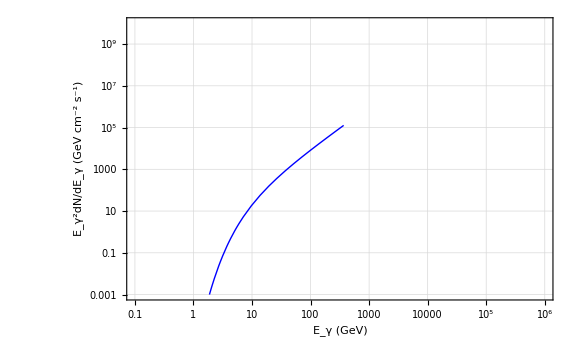

```mathematica
Module[{A,f1,f2,m1,envstyle,minE,maxE,expTicks},
A=2;
m1=81;
f1[x_]:=4/5. fVVqq[x]+1/5. fVVbb[x];
f2=fVVqq;
envstyle={(*Thick,*)Thickness[.01],Opacity[.3,Gray]};
minE=.75;
maxE=30;
expTicks=Table[{10^i,exponentForm[10^i]},{i,-8,-6}];
Show[pW1000,PlotStyle->{
envstyle,
envstyle,
{Thickness[.008],Blue}
},
Filling->{1->{2}},
FillingStyle->{Opacity[.2,Yellow]},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
ImageSize->Large, (* or Large*)
Epilog->{
Text[Rotate[Style["m_χ→ WW",20,Gray],0Degree],ImageScaled@{.25,.85}],
Text[Rotate[Style["m_χ = 1 TeV",20,Gray],0Degree],ImageScaled@{.25,.75}]
(*Text[Rotate[Style["bb",19,Blue],0Degree],ImageScaled@{.27,.92}],
Text[Rotate[Style["m_χ=40 GeV",17,Blue],0Degree],ImageScaled@{.27,.78}],
Text[Rotate[Style["VV (V→qq)",19,Red],0Degree],ImageScaled@{.83,.84}],
Text[Rotate[Style["m_χ=81, m_V=21 GeV",17,Red],0Degree],ImageScaled@{.82,.76}],
Text[Rotate[Style["3φ (φ→bb)",19,Darker[Green]],0Degree],ImageScaled@{.5,.55}],
Text[Rotate[Style["m_χ=123, m_φ=27 GeV",17,Darker[Green]],0Degree],ImageScaled@{.5,.45}],
Text[Style["a=2",19,Gray],ImageScaled@{.2,.23}]*)
}
(*PlotLegends->Placed[LineLegend[Range[1,6],LegendLayout->{"Row",2}],{.35,.25}]*)
(*PlotTheme->"Detailed"*)
]]
```

### mDM = 10 TeV

```mathematica
injSpectrumWW10000 = Table[10^(1/energies[[i]] EGgammaFluxDec["W","noUV"][10000,10^-26,Log[10,energies[[i]]]]),{i,1,Length[energies]}];
```

```mathematica
energies^2*injSpectrumWW10000
```

{1.38929×10^-56,9.01758×10^-52,2.26373×10^-47,2.38742×10^-43,1.14079×10^-39,2.64614×10^-36,3.17319×10^-33,2.08356×10^-30,7.89495×10^-28,1.81111×10^-25,2.6278×10^-23,2.50979×10^-21,1.6365×10^-19,7.53161×10^-18,2.52204×10^-16,6.31765×10^-15,1.21422×10^-13,1.8324×10^-12,2.21763×10^-11,2.19415×10^-10,1.80629×10^-9,1.25727×10^-8,7.5084×10^-8,3.89895×10^-7,1.78213×10^-6,7.25037×10^-6,0.0000265233,0.000088059,0.000267592,0.000750048,0.00195294,0.00475428,0.0108847,0.0235629,0.0484679,0.0951579,0.179049,0.324084,0.566232,0.957924,1.57364,2.51682,3.92826,5.99646,8.97008,13.1731,19.0235,27.0558,37.9483,52.5572,71.9576,97.4944,130.844,174.091,229.821,301.236,392.293,507.877,654.015,838.132,1069.36,1358.96,1720.72,2171.64,2732.56,3429.05,4292.51,5361.43,6682.99,8315.02,10328.3,12809.8,15865.6,19625.9,24250.,29932.8,36912.8,45481.8,55997.,68894.8,84709.4,104094.,127847.,156944.,192580.,236215.,289631.,355012.,435023.,532924.,652699.,799220.,978438.,1.19763×10^6,1.4657×10^6,1.79351×10^6,2.19435×10^6,2.68444×10^6,3.28361×10^6,4.01611×10^6,4.91151×10^6,6.00598×10^6,7.3437×10^6,8.97862×10^6,1.09767×10^7,1.34183×10^7,1.64015×10^7,2.00457×10^7,2.44891×10^7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
pW10000=LogLogPlot[Interpolation[Thread[{energies,energies^2 injSpectrumWW10000}]][x],{x,10^-1,10^5},
PlotRange->{{10^-1,10^5},{10^4,10^8}},
PlotStyle->{Blue,Thick},
FrameTicks->ticks
];
```

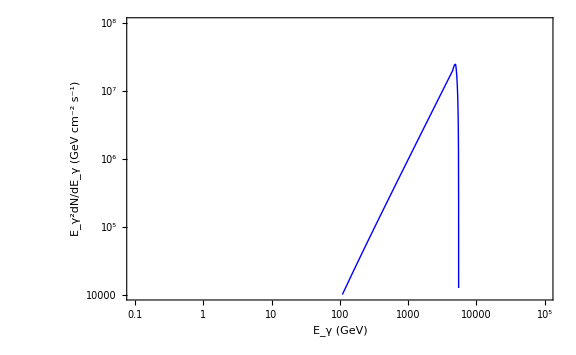

```mathematica
Show[pW10000,
Axes->False,
Frame->True,
FrameStyle-> Thickness[0.004],
FrameTicksStyle-> Thickness[0.004],
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
LabelStyle-> Directive[Bold,Black,FontFamily-> "Helvetica",FontSize-> 14],
ImageSize->Large
]
```

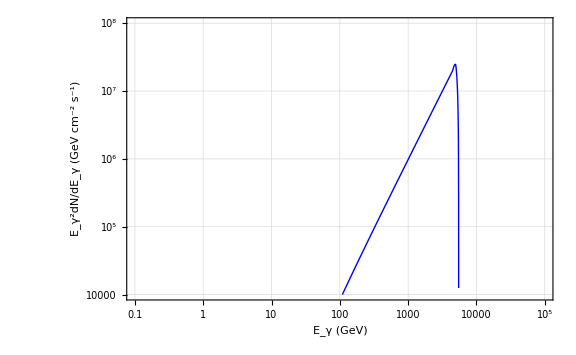

```mathematica
Module[{A,f1,f2,m1,envstyle,minE,maxE,expTicks},
A=2;
m1=81;
f1[x_]:=4/5. fVVqq[x]+1/5. fVVbb[x];
f2=fVVqq;
envstyle={(*Thick,*)Thickness[.01],Opacity[.3,Gray]};
minE=.75;
maxE=30;
expTicks=Table[{10^i,exponentForm[10^i]},{i,-8,-6}];
Show[pW10000,PlotStyle->{
envstyle,
envstyle,
{Thickness[.008],Blue}
},
Filling->{1->{2}},
FillingStyle->{Opacity[.2,Yellow]},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
ImageSize->Large, (* or Large*)
Epilog->{
Text[Rotate[Style["m_χ→ WW",20,Gray],0Degree],ImageScaled@{.25,.85}],
Text[Rotate[Style["m_χ = 10 TeV",20,Gray],0Degree],ImageScaled@{.25,.75}]
(*Text[Rotate[Style["bb",19,Blue],0Degree],ImageScaled@{.27,.92}],
Text[Rotate[Style["m_χ=40 GeV",17,Blue],0Degree],ImageScaled@{.27,.78}],
Text[Rotate[Style["VV (V→qq)",19,Red],0Degree],ImageScaled@{.83,.84}],
Text[Rotate[Style["m_χ=81, m_V=21 GeV",17,Red],0Degree],ImageScaled@{.82,.76}],
Text[Rotate[Style["3φ (φ→bb)",19,Darker[Green]],0Degree],ImageScaled@{.5,.55}],
Text[Rotate[Style["m_χ=123, m_φ=27 GeV",17,Darker[Green]],0Degree],ImageScaled@{.5,.45}],
Text[Style["a=2",19,Gray],ImageScaled@{.2,.23}]*)
}
(*PlotLegends->Placed[LineLegend[Range[1,6],LegendLayout->{"Row",2}],{.35,.25}]*)
(*PlotTheme->"Detailed"*)
]]
```

### mDM = 100 TeV

```mathematica
injSpectrumWW100000 = Table[10^(1/energies[[i]] EGgammaFluxDec["W","noUV"][100000,10^-26,Log[10,energies[[i]]]]),{i,1,Length[energies]}];
```

```mathematica
pW100000=LogLogPlot[Interpolation[Thread[{energies,energies^2 injSpectrumWW100000}]][x],{x,10^-1,10^6},
PlotRange->{{10^-1,10^6},{10^6,10^10}},
PlotStyle->{Blue,Thick},
FrameTicks->ticks
];
```

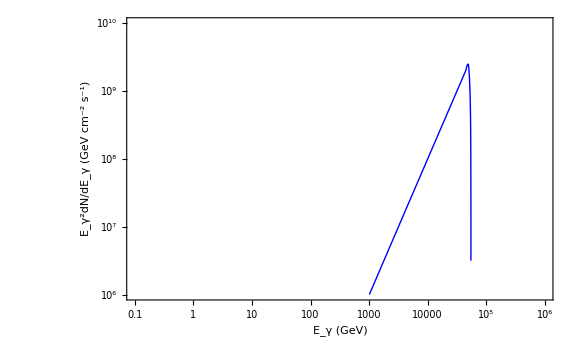

```mathematica
Show[pW100000,
Axes->False,
Frame->True,
FrameStyle-> Thickness[0.004],
FrameTicksStyle-> Thickness[0.004],
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
LabelStyle-> Directive[Bold,Black,FontFamily-> "Helvetica",FontSize-> 14],
ImageSize->Large
]
```

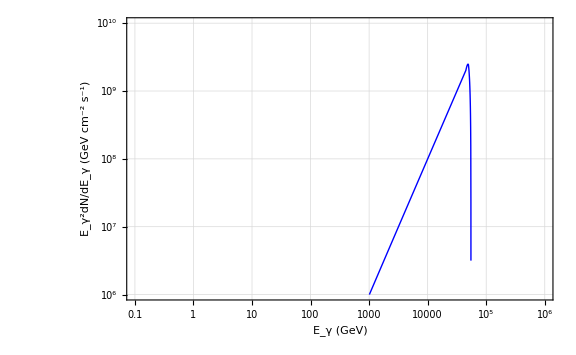

```mathematica
Module[{A,f1,f2,m1,envstyle,minE,maxE,expTicks},
A=2;
m1=81;
f1[x_]:=4/5. fVVqq[x]+1/5. fVVbb[x];
f2=fVVqq;
envstyle={(*Thick,*)Thickness[.01],Opacity[.3,Gray]};
minE=.75;
maxE=30;
expTicks=Table[{10^i,exponentForm[10^i]},{i,-8,-6}];
Show[pW100000,PlotStyle->{
envstyle,
envstyle,
{Thickness[.008],Blue}
},
Filling->{1->{2}},
FillingStyle->{Opacity[.2,Yellow]},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
ImageSize->Large, (* or Large*)
Epilog->{
Text[Rotate[Style["m_χ→ WW",20,Gray],0Degree],ImageScaled@{.25,.85}],
Text[Rotate[Style["m_χ = 100 TeV",20,Gray],0Degree],ImageScaled@{.25,.75}]
(*Text[Rotate[Style["bb",19,Blue],0Degree],ImageScaled@{.27,.92}],
Text[Rotate[Style["m_χ=40 GeV",17,Blue],0Degree],ImageScaled@{.27,.78}],
Text[Rotate[Style["VV (V→qq)",19,Red],0Degree],ImageScaled@{.83,.84}],
Text[Rotate[Style["m_χ=81, m_V=21 GeV",17,Red],0Degree],ImageScaled@{.82,.76}],
Text[Rotate[Style["3φ (φ→bb)",19,Darker[Green]],0Degree],ImageScaled@{.5,.55}],
Text[Rotate[Style["m_χ=123, m_φ=27 GeV",17,Darker[Green]],0Degree],ImageScaled@{.5,.45}],
Text[Style["a=2",19,Gray],ImageScaled@{.2,.23}]*)
}
(*PlotLegends->Placed[LineLegend[Range[1,6],LegendLayout->{"Row",2}],{.35,.25}]*)
(*PlotTheme->"Detailed"*)
]]
```

Attenuation

## Cutoff Power Law

```mathematica
attenuatedSpectrum = GCascadeAttenuate[injSpectrum,0.00001];//AbsoluteTiming
```

Injected spectrum properly formatted

{0.017812,Null}

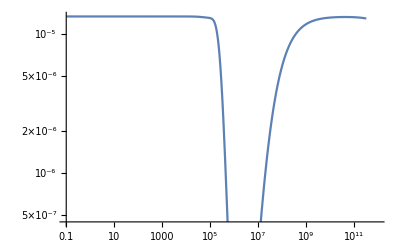

```mathematica
attenuatedSpectrumPlot = specPlot[attenuatedSpectrum]
```

```mathematica
attenuatedSpectrum2 = GCascadeAttenuate[injSpectrum,0.0001];//AbsoluteTiming
```

Injected spectrum properly formatted

{0.032171,Null}

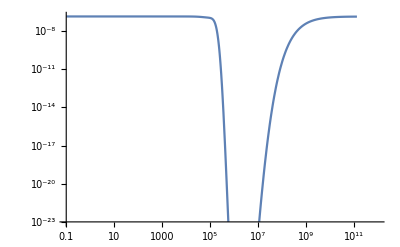

```mathematica
attenuatedSpectrumPlot2 = specPlot[attenuatedSpectrum2]
```

```mathematica
attenuatedSpectrumDMtoBB = GCascadeAttenuate[injSpectrumDMtoBB,0.0001];//AbsoluteTiming
```

Injected spectrum properly formatted

{0.023261,Null}

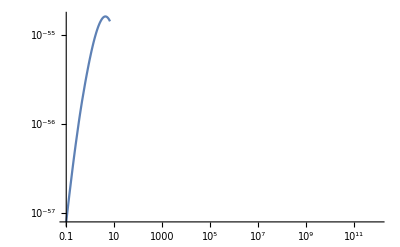

```mathematica
attenuatedSpectrumDMtoBBPlot = specPlot[attenuatedSpectrumDMtoBB]
```

## bb Decay Mode

### -------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------- mDM = 100 GeV --------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

```mathematica
attenuatedSpectrumBB100 = Table[GCascadeAttenuate[injSpectrumBB100,diffuseDistances[[j]]][[i]],{j,1,10},{i,1,Length[GCascadeAttenuate[injSpectrumBB100,0.0001]]}];
```

Injected spectrum properly formatted

Injected spectrum properly formatted

Injected spectrum properly formatted

«3007 more identical outputs»

```mathematica
attenuatedSpectrumBB100[[2]]
```

{1.97854×10^-52,2.05361×10^-52,2.12322×10^-52,2.1864×10^-52,2.24222×10^-52,2.2898×10^-52,2.32834×10^-52,2.35729×10^-52,2.37559×10^-52,2.38233×10^-52,2.37707×10^-52,2.35931×10^-52,2.32891×10^-52,2.28609×10^-52,2.23081×10^-52,2.1637×10^-52,2.08582×10^-52,1.99843×10^-52,1.90441×10^-52,1.80663×10^-52,1.70762×10^-52,1.60796×10^-52,1.5074×10^-52,1.40574×10^-52,1.30311×10^-52,1.20048×10^-52,1.09886×10^-52,9.99152×10^-53,9.01711×10^-53,8.07953×10^-53,7.18673×10^-53,6.33629×10^-53,5.5349×10^-53,4.7907×10^-53,4.10991×10^-53,3.48796×10^-53,2.92715×10^-53,2.42818×10^-53,1.98938×10^-53,1.60972×10^-53,1.28599×10^-53,1.01386×10^-53,7.88407×10^-54,6.043×10^-54,4.56203×10^-54,3.3895×10^-54,2.47889×10^-54,1.78364×10^-54,1.26126×10^-54,8.75296×10^-55,5.95174×10^-55,3.95787×10^-55,2.56699×10^-55,1.62489×10^-55,1.00644×10^-55,6.1336×10^-56,3.69502×10^-56,2.22106×10^-56,1.33954×10^-56,7.96406×10^-57,4.40153×10^-57,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
pBAttenuated100 = Table[LogLogPlot[Interpolation[Thread[{energies,energies^2 attenuatedSpectrumBB100[[i]]}]][x],{x,10^-1,10^4},
PlotRange-> {{10^-1,10^4},{10^-56,10^-50}},
PlotStyle-> {Hue[1/(2i)], Thick},
FrameTicks-> ticks
],{i,1,10}];
```

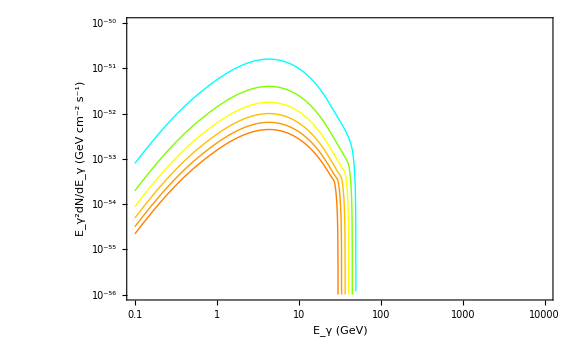

```mathematica
Show[pBAttenuated100[[1]],pBAttenuated100[[2]],pBAttenuated100[[3]],pBAttenuated100[[4]],pBAttenuated100[[5]],pBAttenuated100[[6]],
Axes->False,
Frame-> True,
FrameStyle-> Thickness[0.004],
FrameTicksStyle-> Thickness[0.004],
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
LabelStyle-> Directive[Bold,Black,FontFamily-> "Helvetica",FontSize-> 14],
ImageSize->Large
]
```

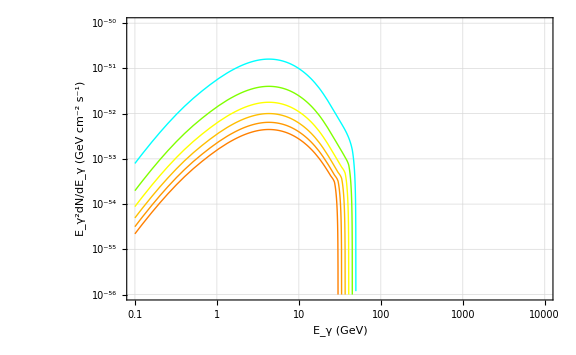

```mathematica
Module[{A,f1,f2,m1,envstyle,minE,maxE,expTicks},
A=2;
m1=81;
f1[x_]:=4/5. fVVqq[x]+1/5. fVVbb[x];
f2=fVVqq;
envstyle={(*Thick,*)Thickness[.01],Opacity[.3,Gray]};
minE=.75;
maxE=30;
expTicks=Table[{10^i,exponentForm[10^i]},{i,-8,-6}];
Show[pBAttenuated100[[1]],pBAttenuated100[[2]],pBAttenuated100[[3]],pBAttenuated100[[4]],pBAttenuated100[[5]],pBAttenuated100[[6]],PlotStyle->{
envstyle,
envstyle,
{Thickness[.008],Blue}
},
Filling->{1->{2}},
FillingStyle->{Opacity[.2,Yellow]},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
ImageSize->Large, (* or Large*)
Epilog->{
Text[Rotate[Style["m_χ→ bb",20,Gray],0Degree],ImageScaled@{.75,.25}],
Text[Rotate[Style["m_χ = 100 GeV",20,Gray],0Degree],ImageScaled@{.75,.15}]
(*Text[Rotate[Style["bb",19,Blue],0Degree],ImageScaled@{.27,.92}],
Text[Rotate[Style["m_χ=40 GeV",17,Blue],0Degree],ImageScaled@{.27,.78}],
Text[Rotate[Style["VV (V→qq)",19,Red],0Degree],ImageScaled@{.83,.84}],
Text[Rotate[Style["m_χ=81, m_V=21 GeV",17,Red],0Degree],ImageScaled@{.82,.76}],
Text[Rotate[Style["3φ (φ→bb)",19,Darker[Green]],0Degree],ImageScaled@{.5,.55}],
Text[Rotate[Style["m_χ=123, m_φ=27 GeV",17,Darker[Green]],0Degree],ImageScaled@{.5,.45}],
Text[Style["a=2",19,Gray],ImageScaled@{.2,.23}]*)
}
(*PlotLegends->Placed[LineLegend[Range[1,6],LegendLayout->{"Row",2}],{.35,.25}]*)
(*PlotTheme->"Detailed"*)
]]
```

### -------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------- mDM = 1 TeV --------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

```mathematica
zValues = {0.0001,0.001,0.01,0.1,1};
```

```mathematica
attenuatedSpectrumBB1000 = Table[GCascadeAttenuate[injSpectrumBB1000,diffuseDistances[[j]]][[i]],{j,1,10},{i,1,Length[GCascadeAttenuate[injSpectrumBB100,0.0001]]}];
```

Injected spectrum properly formatted

Injected spectrum properly formatted

Injected spectrum properly formatted

«3007 more identical outputs»

```mathematica
pBAttenuated1000 = Table[LogLogPlot[Interpolation[Thread[{energies,energies^2 attenuatedSpectrumBB1000[[i]]}]][x],{x,10^-1,10^4},
PlotRange-> {{10^-1,10^4},{10^-56,10^-49}},
PlotStyle-> {Hue[1/(2i)], Thick},
FrameTicks-> ticks
],{i,1,10}];
```

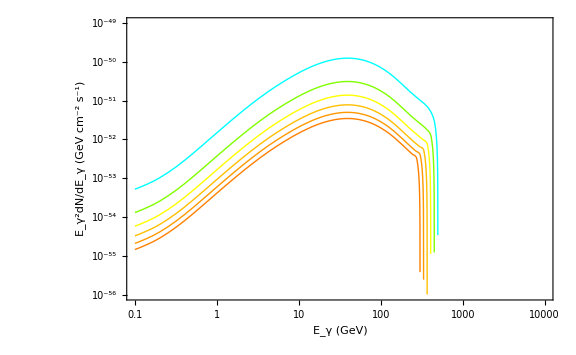

```mathematica
Show[pBAttenuated1000[[1]],pBAttenuated1000[[2]],pBAttenuated1000[[3]],pBAttenuated1000[[4]],pBAttenuated1000[[5]],pBAttenuated1000[[6]],
Axes->False,
Frame-> True,
FrameStyle-> Thickness[0.004],
FrameTicksStyle-> Thickness[0.004],
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
LabelStyle-> Directive[Bold,Black,FontFamily-> "Helvetica",FontSize-> 14],
ImageSize->Large
]
```

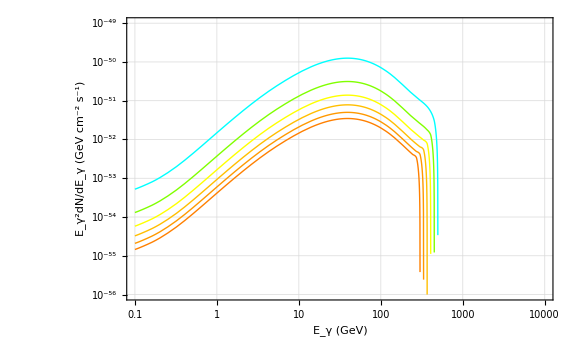

```mathematica
Module[{A,f1,f2,m1,envstyle,minE,maxE,expTicks},
A=2;
m1=81;
f1[x_]:=4/5. fVVqq[x]+1/5. fVVbb[x];
f2=fVVqq;
envstyle={(*Thick,*)Thickness[.01],Opacity[.3,Gray]};
minE=.75;
maxE=30;
expTicks=Table[{10^i,exponentForm[10^i]},{i,-8,-6}];
Show[pBAttenuated1000[[1]],pBAttenuated1000[[2]],pBAttenuated1000[[3]],pBAttenuated1000[[4]],pBAttenuated1000[[5]],pBAttenuated1000[[6]],PlotStyle->{
envstyle,
envstyle,
{Thickness[.008],Blue}
},
Filling->{1->{2}},
FillingStyle->{Opacity[.2,Yellow]},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
ImageSize->Large, (* or Large*)
Epilog->{
Text[Rotate[Style["m_χ→ bb",20,Gray],0Degree],ImageScaled@{.85,.25}],
Text[Rotate[Style["m_χ = 1 TeV",20,Gray],0Degree],ImageScaled@{.85,.15}]
(*Text[Rotate[Style["bb",19,Blue],0Degree],ImageScaled@{.27,.92}],
Text[Rotate[Style["m_χ=40 GeV",17,Blue],0Degree],ImageScaled@{.27,.78}],
Text[Rotate[Style["VV (V→qq)",19,Red],0Degree],ImageScaled@{.83,.84}],
Text[Rotate[Style["m_χ=81, m_V=21 GeV",17,Red],0Degree],ImageScaled@{.82,.76}],
Text[Rotate[Style["3φ (φ→bb)",19,Darker[Green]],0Degree],ImageScaled@{.5,.55}],
Text[Rotate[Style["m_χ=123, m_φ=27 GeV",17,Darker[Green]],0Degree],ImageScaled@{.5,.45}],
Text[Style["a=2",19,Gray],ImageScaled@{.2,.23}]*)
}
(*PlotLegends->Placed[LineLegend[Range[1,6],LegendLayout->{"Row",2}],{.35,.25}]*)
(*PlotTheme->"Detailed"*)
]]
```

### -------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------- mDM = 10 TeV --------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

```mathematica
zValues = {0.0001,0.001,0.01,0.1,1};
```

```mathematica
attenuatedSpectrumBB10000 = Table[GCascadeAttenuate[injSpectrumBB10000,diffuseDistances[[j]]][[i]],{j,1,10},{i,1,Length[GCascadeAttenuate[injSpectrumBB1000,0.0001]]}];
```

Injected spectrum properly formatted

Injected spectrum properly formatted

Injected spectrum properly formatted

«3007 more identical outputs»

```mathematica
pBAttenuated10000 = Table[LogLogPlot[Interpolation[Thread[{energies,energies^2 attenuatedSpectrumBB10000[[i]]}]][x],{x,10^-1,10^4},
PlotRange-> {{10^-1,10^4},{10^-55,10^-48}},
PlotStyle-> {Hue[1/(2i)], Thick},
FrameTicks-> ticks
],{i,1,10}];
```

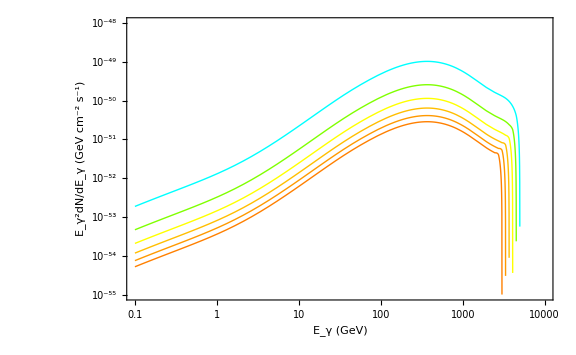

```mathematica
Show[pBAttenuated10000[[1]],pBAttenuated10000[[2]],pBAttenuated10000[[3]],pBAttenuated10000[[4]],pBAttenuated10000[[5]],pBAttenuated10000[[6]],
Axes->False,
Frame-> True,
FrameStyle-> Thickness[0.004],
FrameTicksStyle-> Thickness[0.004],
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
LabelStyle-> Directive[Bold,Black,FontFamily-> "Helvetica",FontSize-> 14],
ImageSize->Large
]
```

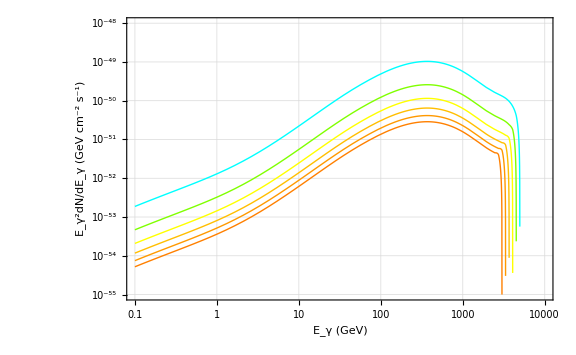

```mathematica
Module[{A,f1,f2,m1,envstyle,minE,maxE,expTicks},
A=2;
m1=81;
f1[x_]:=4/5. fVVqq[x]+1/5. fVVbb[x];
f2=fVVqq;
envstyle={(*Thick,*)Thickness[.01],Opacity[.3,Gray]};
minE=.75;
maxE=30;
expTicks=Table[{10^i,exponentForm[10^i]},{i,-8,-6}];
Show[pBAttenuated10000[[1]],pBAttenuated10000[[2]],pBAttenuated10000[[3]],pBAttenuated10000[[4]],pBAttenuated10000[[5]],pBAttenuated10000[[6]],PlotStyle->{
envstyle,
envstyle,
{Thickness[.008],Blue}
},
Filling->{1->{2}},
FillingStyle->{Opacity[.2,Yellow]},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
ImageSize->Large, (* or Large*)
Epilog->{
Text[Rotate[Style["m_χ→ bb",20,Gray],0Degree],ImageScaled@{.75,.25}],
Text[Rotate[Style["m_χ = 10 TeV",20,Gray],0Degree],ImageScaled@{.75,.15}]
(*Text[Rotate[Style["bb",19,Blue],0Degree],ImageScaled@{.27,.92}],
Text[Rotate[Style["m_χ=40 GeV",17,Blue],0Degree],ImageScaled@{.27,.78}],
Text[Rotate[Style["VV (V→qq)",19,Red],0Degree],ImageScaled@{.83,.84}],
Text[Rotate[Style["m_χ=81, m_V=21 GeV",17,Red],0Degree],ImageScaled@{.82,.76}],
Text[Rotate[Style["3φ (φ→bb)",19,Darker[Green]],0Degree],ImageScaled@{.5,.55}],
Text[Rotate[Style["m_χ=123, m_φ=27 GeV",17,Darker[Green]],0Degree],ImageScaled@{.5,.45}],
Text[Style["a=2",19,Gray],ImageScaled@{.2,.23}]*)
}
(*PlotLegends->Placed[LineLegend[Range[1,6],LegendLayout->{"Row",2}],{.35,.25}]*)
(*PlotTheme->"Detailed"*)
]]
```

## WW Decay Mode

### mDM = 1 TeV

```mathematica
zValues = {0.0001,0.001,0.01,0.1,1};
```

```mathematica
attenuatedSpectrumWW1000 = Table[GCascadeAttenuate[injSpectrumWW1000,diffuseDistances[[j]]][[i]],{j,1,10},{i,1,Length[GCascadeAttenuate[injSpectrumWW1000,0.0001]]}];
```

Injected spectrum properly formatted

Injected spectrum properly formatted

Injected spectrum properly formatted

«3007 more identical outputs»

```mathematica
pWAttenuated1000 = Table[LogLogPlot[Interpolation[Thread[{energies,energies^2 attenuatedSpectrumWW1000[[i]]}]][x],{x,10^-1,10^4},
PlotRange-> {{10^-1,10^4},{10^-56,10^-49}},
PlotStyle-> {Hue[1/(2i)], Thick},
FrameTicks-> ticks
],{i,1,10}];
```

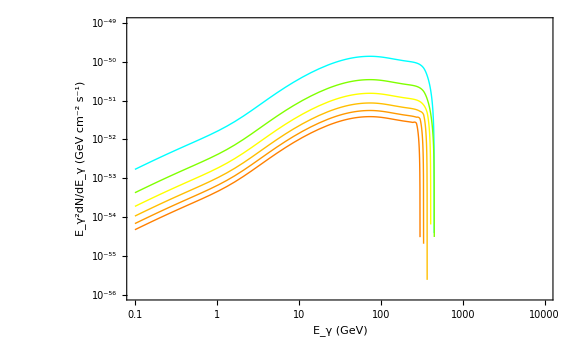

```mathematica
Show[pWAttenuated1000[[1]],pWAttenuated1000[[2]],pWAttenuated1000[[3]],pWAttenuated1000[[4]],pWAttenuated1000[[5]],pWAttenuated1000[[6]],
Axes->False,
Frame-> True,
FrameStyle-> Thickness[0.004],
FrameTicksStyle-> Thickness[0.004],
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
LabelStyle-> Directive[Bold,Black,FontFamily-> "Helvetica",FontSize-> 14],
ImageSize->Large
]
```

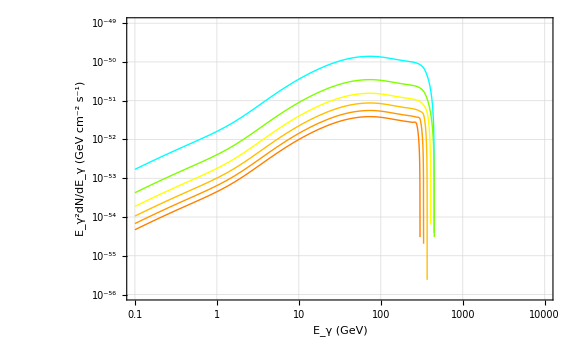

```mathematica
Module[{A,f1,f2,m1,envstyle,minE,maxE,expTicks},
A=2;
m1=81;
f1[x_]:=4/5. fVVqq[x]+1/5. fVVbb[x];
f2=fVVqq;
envstyle={(*Thick,*)Thickness[.01],Opacity[.3,Gray]};
minE=.75;
maxE=30;
expTicks=Table[{10^i,exponentForm[10^i]},{i,-8,-6}];
Show[pWAttenuated1000[[1]],pWAttenuated1000[[2]],pWAttenuated1000[[3]],pWAttenuated1000[[4]],pWAttenuated1000[[5]],pWAttenuated1000[[6]],PlotStyle->{
envstyle,
envstyle,
{Thickness[.008],Blue}
},
Filling->{1->{2}},
FillingStyle->{Opacity[.2,Yellow]},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
ImageSize->Large, (* or Large*)
Epilog->{
Text[Rotate[Style["m_χ→ WW",20,Gray],0Degree],ImageScaled@{.85,.25}],
Text[Rotate[Style["m_χ = 1 TeV",20,Gray],0Degree],ImageScaled@{.85,.15}]
(*Text[Rotate[Style["bb",19,Blue],0Degree],ImageScaled@{.27,.92}],
Text[Rotate[Style["m_χ=40 GeV",17,Blue],0Degree],ImageScaled@{.27,.78}],
Text[Rotate[Style["VV (V→qq)",19,Red],0Degree],ImageScaled@{.83,.84}],
Text[Rotate[Style["m_χ=81, m_V=21 GeV",17,Red],0Degree],ImageScaled@{.82,.76}],
Text[Rotate[Style["3φ (φ→bb)",19,Darker[Green]],0Degree],ImageScaled@{.5,.55}],
Text[Rotate[Style["m_χ=123, m_φ=27 GeV",17,Darker[Green]],0Degree],ImageScaled@{.5,.45}],
Text[Style["a=2",19,Gray],ImageScaled@{.2,.23}]*)
}
(*PlotLegends->Placed[LineLegend[Range[1,6],LegendLayout->{"Row",2}],{.35,.25}]*)
(*PlotTheme->"Detailed"*)
]]
```

```mathematica
"
```

EM Cascades from a Point Source

```mathematica
pointSourceSpectrum = GCascadePoint[injSpectrum,0.1];//AbsoluteTiming
```

Injected spectrum properly formatted

{45.4489,Null}

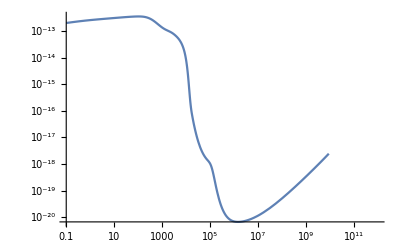

-Graphics-

```mathematica
pointSourceSpectrumPlot= specPlot[pointSourceSpectrum]
Show[pointSourceSpectrumPlot,attenuatedSpectrumPlot]
```

```mathematica
pointSourceSpectrumDMtoBB = GCascadePoint[injSpectrumDMtoBB,0.01];//AbsoluteTiming
```

Injected spectrum properly formatted

{0.851197,Null}

```mathematica
pointSourceSpectrumDMtoWW = GCascadePoint[injSpectrumDMtoWW,0.01];//AbsoluteTiming
```

Injected spectrum properly formatted

{6.21049,Null}

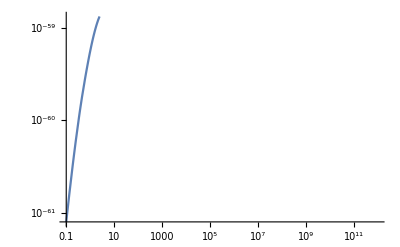

```mathematica
pointSourceSpectrumDMtoBBPlot = specPlot[pointSourceSpectrumDMtoBB]
```

```mathematica
p1PointSource=LogLogPlot[Interpolation[Thread[{energies,energies^2 pointSourceSpectrumDMtoBB}]][x],{x,10^-3,10^4},
PlotRange->{{10^-3,10^4},{10^-60,10^-57}},
PlotStyle->{Red,Thick},
FrameTicks->ticks
];
```

```mathematica
p2PointSource=LogLogPlot[Interpolation[Thread[{energies,energies^2 pointSourceSpectrumDMtoWW}]][x],{x,10^-3,10^4},
PlotRange->{{10^-3,10^4},{10^-60,10^-57}},
PlotStyle->{Blue,Thick},
FrameTicks->ticks
];
```

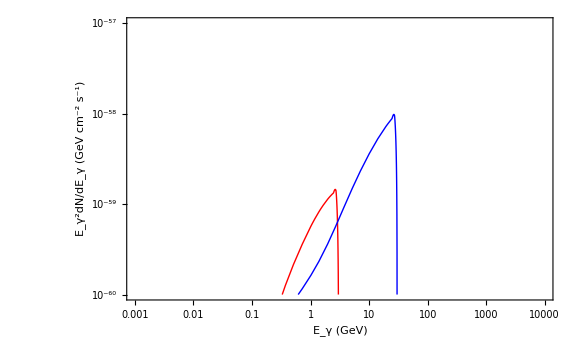

```mathematica
Show[p1PointSource,p2PointSource,
Axes->False,
Frame->True,
FrameStyle-> Thickness[0.004],
FrameTicksStyle-> Thickness[0.004],
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
LabelStyle-> Directive[Bold,Black,FontFamily-> "Helvetica",FontSize-> 14],
ImageSize->Large
]
```

Diffuse Gamma-Ray Background from a Non-evolving Population of Sources

```mathematica
Mpc = 3.086*10^24; (*cm*)
ρz=ConstantArray[0.0,Length[diffuseDistances]]; (*creates array*)
ρz[[1;;100]]=Table[5.0*10^-6*(Mpc)^-3,{i,1,100}]; (*sets the first 46 members*)
ρ=Thread[{diffuseDistances,ρz}];
```

```mathematica
ρz2=ConstantArray[0.0,Length[diffuseDistances]]; (*creates array*)
ρz2[[1;;100]]=Table[5.0*10^-6*(Mpc)^-3*(1+diffuseDistances[[i]])^3,{i,1,100}]; (*sets the first 46 members*)
ρ2=Thread[{diffuseDistances,ρz2}];
```

```mathematica
diffuseDistances[[23]]
```

0.0005

```mathematica
diffuseDistances[[46]]
```

0.1

```mathematica
diffuseDistances[[100]]
```

0.64

## bb Decay Mode

### mDM = 100 GeV

```mathematica
diffuseConstantBackgroundSpectrumBB100z23 = GCascadeDiffuseConstant[injSpectrumBB100,diffuseDistances[[23]],ρ];//AbsoluteTiming
```

Injected spectrum properly formatted

Successfully incorporated luminosity function. GCascade will produce spectra for diffuse background generated by your injected spectra.

{0.716319,Null}

```mathematica
diffuseDistances[[23]]
```

0.0005

```mathematica
diffuseConstantBackgroundSpectrumBB100z46 = GCascadeDiffuseConstant[injSpectrumBB100,diffuseDistances[[46]],ρ];//AbsoluteTiming
```

Injected spectrum properly formatted

Successfully incorporated luminosity function. GCascade will produce spectra for diffuse background generated by your injected spectra.

{45.8045,Null}

```mathematica
diffuseDistances[[46]]
```

0.1

```mathematica
diffuseConstantBackgroundSpectrumBB100z100 = GCascadeDiffuseConstant[injSpectrumBB100,diffuseDistances[[100]],ρ];//AbsoluteTiming
```

Injected spectrum properly formatted

Successfully incorporated luminosity function. GCascade will produce spectra for diffuse background generated by your injected spectra.

{282.444,Null}

```mathematica
pBDiffuseConstantBackground100z23 = LogLogPlot[Interpolation[Thread[{energies,energies^2 diffuseConstantBackgroundSpectrumBB100z23}]][x],{x,10^-3,10^4},
PlotRange-> {{10^-3,10^4},{10^-64,10^-57}},
PlotStyle-> {Hue[1], Thick},
FrameTicks-> ticks
];
```

```mathematica
pBDiffuseConstantBackground100z46 = LogLogPlot[Interpolation[Thread[{energies,energies^2 diffuseConstantBackgroundSpectrumBB100z46}]][x],{x,10^-3,10^4},
PlotRange-> {{10^-3,10^4},{10^-64,10^-57}},
PlotStyle-> {Hue[1/2], Thick},
FrameTicks-> ticks
];
```

```mathematica
pBDiffuseConstantBackground100z100 = LogLogPlot[Interpolation[Thread[{energies,energies^2 diffuseConstantBackgroundSpectrumBB100z100}]][x],{x,10^-3,10^4},
PlotRange-> {{10^-3,10^4},{10^-64,10^-57}},
PlotStyle-> {Hue[1/3], Thick},
FrameTicks-> ticks
];
```

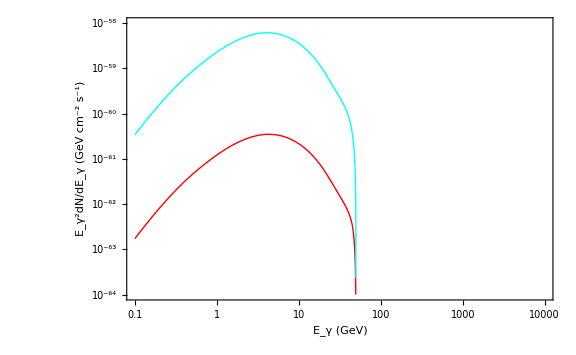

```mathematica
Show[pBDiffuseConstantBackground100z23,pBDiffuseConstantBackground100z46,
Axes->False,
Frame-> True,
FrameStyle-> Thickness[0.004],
FrameTicksStyle-> Thickness[0.004],
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
LabelStyle-> Directive[Bold,Black,FontFamily-> "Helvetica",FontSize-> 14],
ImageSize->Large
]
```

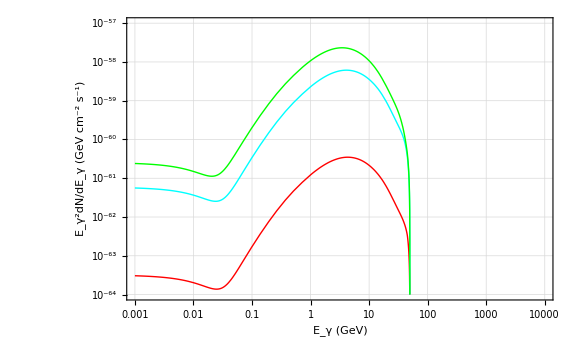

```mathematica
Module[{A,f1,f2,m1,envstyle,minE,maxE,expTicks},
A=2;
m1=81;
f1[x_]:=4/5. fVVqq[x]+1/5. fVVbb[x];
f2=fVVqq;
envstyle={(*Thick,*)Thickness[.01],Opacity[.3,Gray]};
minE=.75;
maxE=30;
expTicks=Table[{10^i,exponentForm[10^i]},{i,-8,-6}];
Show[pBDiffuseConstantBackground100z23,pBDiffuseConstantBackground100z46,pBDiffuseConstantBackground100z100,PlotStyle->{
envstyle,
envstyle,
{Thickness[.008],Blue}
},
Filling->{1->{2}},
FillingStyle->{Opacity[.2,Yellow]},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
ImageSize->Large, (* or Large*)
Epilog->{
Text[Rotate[Style["m_χ→ bb",20,Gray],0Degree],ImageScaled@{.80,.25}],
Text[Rotate[Style["m_χ = 100 GeV",20,Gray],0Degree],ImageScaled@{.82,.15}]
(*Text[Rotate[Style["bb",19,Blue],0Degree],ImageScaled@{.27,.92}],
Text[Rotate[Style["m_χ=40 GeV",17,Blue],0Degree],ImageScaled@{.27,.78}],
Text[Rotate[Style["VV (V→qq)",19,Red],0Degree],ImageScaled@{.83,.84}],
Text[Rotate[Style["m_χ=81, m_V=21 GeV",17,Red],0Degree],ImageScaled@{.82,.76}],
Text[Rotate[Style["3φ (φ→bb)",19,Darker[Green]],0Degree],ImageScaled@{.5,.55}],
Text[Rotate[Style["m_χ=123, m_φ=27 GeV",17,Darker[Green]],0Degree],ImageScaled@{.5,.45}],
Text[Style["a=2",19,Gray],ImageScaled@{.2,.23}]*)
}
(*PlotLegends->Placed[LineLegend[Range[1,6],LegendLayout->{"Row",2}],{.35,.25}]*)
(*PlotTheme->"Detailed"*)
]]
```

#### With Redshift Dependence in ρ(z)

```mathematica
diffuseConstantBackgroundSpectrumBB100z23Redshift = GCascadeDiffuseConstant[injSpectrumBB100,diffuseDistances[[23]],ρ2];//AbsoluteTiming
```

Injected spectrum properly formatted

Successfully incorporated luminosity function. GCascade will produce spectra for diffuse background generated by your injected spectra.

{0.264612,Null}

```mathematica
diffuseConstantBackgroundSpectrumBB100z46Redshift = GCascadeDiffuseConstant[injSpectrumBB100,diffuseDistances[[46]],ρ2];//AbsoluteTiming
```

Injected spectrum properly formatted

Successfully incorporated luminosity function. GCascade will produce spectra for diffuse background generated by your injected spectra.

{46.1903,Null}

```mathematica
diffuseConstantBackgroundSpectrumBB100z100Redshift = GCascadeDiffuseConstant[injSpectrumBB100,diffuseDistances[[100]],ρ2];//AbsoluteTiming
```

Injected spectrum properly formatted

Successfully incorporated luminosity function. GCascade will produce spectra for diffuse background generated by your injected spectra.

{340.778,Null}

```mathematica
pBDiffuseConstantBackground100z23Redshift = LogLogPlot[Interpolation[Thread[{energies,energies^2 diffuseConstantBackgroundSpectrumBB100z23Redshift}]][x],{x,10^-3,10^4},
PlotRange-> {{10^-3,10^4},{10^-55,10^-48}},
PlotStyle-> {Hue[1], Thick},
FrameTicks-> ticks
];
```

```mathematica
pBDiffuseConstantBackground100z46Redshift = LogLogPlot[Interpolation[Thread[{energies,energies^2 diffuseConstantBackgroundSpectrumBB100z46Redshift}]][x],{x,10^-3,10^4},
PlotRange-> {{10^-3,10^4},{10^-55,10^-48}},
PlotStyle-> {Hue[1/2], Thick},
FrameTicks-> ticks
];
```

```mathematica
pBDiffuseConstantBackground100z100Redshift = LogLogPlot[Interpolation[Thread[{energies,energies^2 diffuseConstantBackgroundSpectrumBB100z100Redshift}]][x],{x,10^-3,10^4},
PlotRange-> {{10^-3,10^4},{10^-55,10^-48}},
PlotStyle-> {Hue[1/3], Thick},
FrameTicks-> ticks
];
```

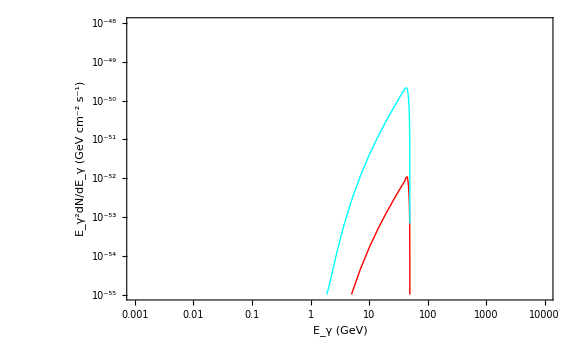

```mathematica
Show[pBDiffuseConstantBackground100z23Redshift,pBDiffuseConstantBackground100z46Redshift,
Axes->False,
Frame-> True,
FrameStyle-> Thickness[0.004],
FrameTicksStyle-> Thickness[0.004],
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
LabelStyle-> Directive[Bold,Black,FontFamily-> "Helvetica",FontSize-> 14],
ImageSize->Large
]
```

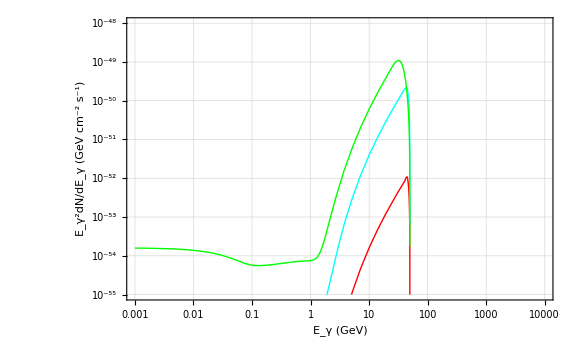

```mathematica
Module[{A,f1,f2,m1,envstyle,minE,maxE,expTicks},
A=2;
m1=81;
f1[x_]:=4/5. fVVqq[x]+1/5. fVVbb[x];
f2=fVVqq;
envstyle={(*Thick,*)Thickness[.01],Opacity[.3,Gray]};
minE=.75;
maxE=30;
expTicks=Table[{10^i,exponentForm[10^i]},{i,-8,-6}];
Show[pBDiffuseConstantBackground100z23Redshift,pBDiffuseConstantBackground100z46Redshift,pBDiffuseConstantBackground100z100Redshift,PlotStyle->{
envstyle,
envstyle,
{Thickness[.008],Blue}
},
Filling->{1->{2}},
FillingStyle->{Opacity[.2,Yellow]},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
ImageSize->Large, (* or Large*)
Epilog->{
Text[Rotate[Style["m_χ→ bb",20,Gray],0Degree],ImageScaled@{.80,.25}],
Text[Rotate[Style["m_χ = 100 GeV",20,Gray],0Degree],ImageScaled@{.82,.15}]
(*Text[Rotate[Style["bb",19,Blue],0Degree],ImageScaled@{.27,.92}],
Text[Rotate[Style["m_χ=40 GeV",17,Blue],0Degree],ImageScaled@{.27,.78}],
Text[Rotate[Style["VV (V→qq)",19,Red],0Degree],ImageScaled@{.83,.84}],
Text[Rotate[Style["m_χ=81, m_V=21 GeV",17,Red],0Degree],ImageScaled@{.82,.76}],
Text[Rotate[Style["3φ (φ→bb)",19,Darker[Green]],0Degree],ImageScaled@{.5,.55}],
Text[Rotate[Style["m_χ=123, m_φ=27 GeV",17,Darker[Green]],0Degree],ImageScaled@{.5,.45}],
Text[Style["a=2",19,Gray],ImageScaled@{.2,.23}]*)
}
(*PlotLegends->Placed[LineLegend[Range[1,6],LegendLayout->{"Row",2}],{.35,.25}]*)
(*PlotTheme->"Detailed"*)
]]
```

Injected spectrum properly formatted

Successfully incorporated luminosity function. GCascade will produce spectra for diffuse background generated by your injected spectra.

{284.19,Null}

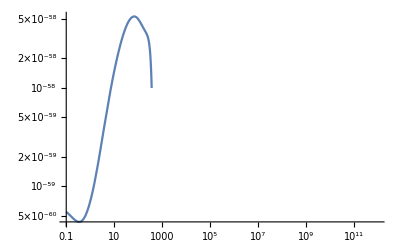

```mathematica
diffuseConstantBackgroundSpectrumDMtoWW = GCascadeDiffuseConstant[injSpectrumDMtoWW,diffuseDistances[[46]],ρ];//AbsoluteTiming
diffuseConstantBackgroundSpectrumDMtoWWPlot = specPlot[diffuseConstantBackgroundSpectrumDMtoWW]
```

```mathematica
firstStep = Table[If[i==0,Table[10^-6*10^i,{j,1,10}],Table[10^-6*10^i,{j,1,9}]]//N,{i,0,4}]//Flatten;
diffuseDistances[[3]]
```

3.×10^-6

```mathematica
p1ConstantBackground=LogLogPlot[Interpolation[Thread[{energies,energies^2 diffuseConstantBackgroundSpectrumDMtoBB}]][x],{x,10^-3,10^4},
PlotRange->{{10^-3,10^4},{10^-60,10^-57}},
PlotStyle->{Red,Thick},
FrameTicks->ticks
];
```

```mathematica
p2ConstantBackground=LogLogPlot[Interpolation[Thread[{energies,energies^2 diffuseConstantBackgroundSpectrumDMtoWW}]][x],{x,10^-3,10^4},
PlotRange->{{10^-3,10^4},{10^-60,10^-57}},
PlotStyle->{Blue,Thick},
FrameTicks->ticks
];
```

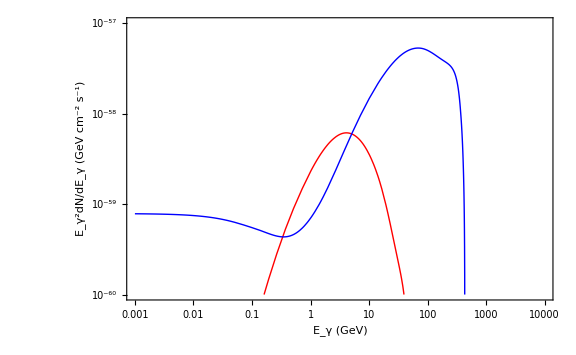

```mathematica
Show[p1ConstantBackground,p2ConstantBackground,
Axes->False,
Frame->True,
FrameStyle-> Thickness[0.004],
FrameTicksStyle-> Thickness[0.004],
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
LabelStyle-> Directive[Bold,Black,FontFamily-> "Helvetica",FontSize-> 14],
ImageSize->Large
]
```

```mathematica
diffuseDistances[[28]]
```

0.001

### ----------------------------------------------------------------------------------------------------------------------------------------------------------------------- mDM = 1 TeV -----------------------------------------------------------------------------------------------------------------------------------------------------------------------

```mathematica
diffuseConstantBackgroundSpectrumBB1000z23 = GCascadeDiffuseConstant[injSpectrumBB1000,diffuseDistances[[23]],ρ];//AbsoluteTiming
```

Injected spectrum properly formatted

Successfully incorporated luminosity function. GCascade will produce spectra for diffuse background generated by your injected spectra.

{0.273017,Null}

```mathematica
diffuseDistances[[23]]
```

0.0005

```mathematica
diffuseConstantBackgroundSpectrumBB1000z46 = GCascadeDiffuseConstant[injSpectrumBB1000,diffuseDistances[[46]],ρ];//AbsoluteTiming
```

{41.5731,Null}

Successfully incorporated luminosity function. GCascade will produce spectra for diffuse background generated by your injected spectra.

Injected spectrum properly formatted

Injected spectrum properly formatted

Successfully incorporated luminosity function. GCascade will produce spectra for diffuse background generated by your injected spectra.

{45.8045,Null}

```mathematica
pBDiffuseConstantBackground1000z23 = LogLogPlot[Interpolation[Thread[{energies,energies^2 diffuseConstantBackgroundSpectrumBB1000z23}]][x],{x,10^-1,10^4},
PlotRange-> {{10^-1,10^4},{10^-62,10^-57}},
PlotStyle-> {Hue[1], Thick},
FrameTicks-> ticks
];
```

```mathematica
pBDiffuseConstantBackground1000z46 = LogLogPlot[Interpolation[Thread[{energies,energies^2 diffuseConstantBackgroundSpectrumBB1000z46}]][x],{x,10^-1,10^4},
PlotRange-> {{10^-1,10^4},{10^-62,10^-57}},
PlotStyle-> {Hue[1/2], Thick},
FrameTicks-> ticks
];
```

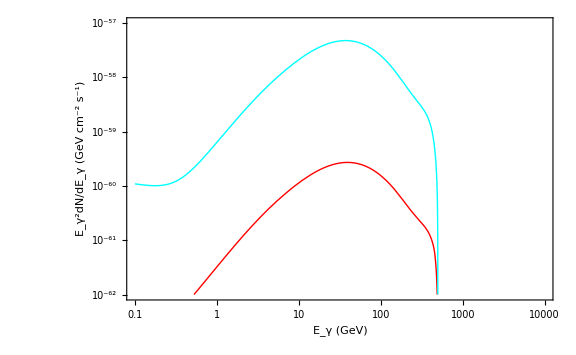

```mathematica
Show[pBDiffuseConstantBackground1000z23,pBDiffuseConstantBackground1000z46,
Axes->False,
Frame-> True,
FrameStyle-> Thickness[0.004],
FrameTicksStyle-> Thickness[0.004],
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
LabelStyle-> Directive[Bold,Black,FontFamily-> "Helvetica",FontSize-> 14],
ImageSize->Large
]
```

```mathematica
Module[{A,f1,f2,m1,envstyle,minE,maxE,expTicks},
A=2;
m1=81;
f1[x_]:=4/5. fVVqq[x]+1/5. fVVbb[x];
f2=fVVqq;
envstyle={(*Thick,*)Thickness[.01],Opacity[.3,Gray]};
minE=.75;
maxE=30;
expTicks=Table[{10^i,exponentForm[10^i]},{i,-8,-6}];
Show[pBDiffuseConstantBackground100000z23,pBDiffuseConstantBackground100000z46,pBDiffuseConstantBackground100000z100,PlotStyle->{
envstyle,
envstyle,
{Thickness[.008],Blue}
},
Filling->{1->{2}},
FillingStyle->{Opacity[.2,Yellow]},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
ImageSize->Large, (* or Large*)
Epilog->{
Text[Rotate[Style["m_χ→ bb",20,Gray],0Degree],ImageScaled@{.80,.25}],
Text[Rotate[Style["m_χ = 100 TeV",20,Gray],0Degree],ImageScaled@{.80,.15}]
(*Text[Rotate[Style["bb",19,Blue],0Degree],ImageScaled@{.27,.92}],
Text[Rotate[Style["m_χ=40 GeV",17,Blue],0Degree],ImageScaled@{.27,.78}],
Text[Rotate[Style["VV (V→qq)",19,Red],0Degree],ImageScaled@{.83,.84}],
Text[Rotate[Style["m_χ=81, m_V=21 GeV",17,Red],0Degree],ImageScaled@{.82,.76}],
Text[Rotate[Style["3φ (φ→bb)",19,Darker[Green]],0Degree],ImageScaled@{.5,.55}],
Text[Rotate[Style["m_χ=123, m_φ=27 GeV",17,Darker[Green]],0Degree],ImageScaled@{.5,.45}],
Text[Style["a=2",19,Gray],ImageScaled@{.2,.23}]*)
}
(*PlotLegends->Placed[LineLegend[Range[1,6],LegendLayout->{"Row",2}],{.35,.25}]*)
(*PlotTheme->"Detailed"*)
]]
```

#### With Redshift Dependence

```mathematica
diffuseConstantBackgroundSpectrumBB1000z23Redshift = GCascadeDiffuseConstant[injSpectrumBB1000,diffuseDistances[[23]],ρ2];//AbsoluteTiming
```

Injected spectrum properly formatted

Successfully incorporated luminosity function. GCascade will produce spectra for diffuse background generated by your injected spectra.

{0.275571,Null}

```mathematica
diffuseConstantBackgroundSpectrumBB1000z46Redshift = GCascadeDiffuseConstant[injSpectrumBB1000,diffuseDistances[[46]],ρ2];//AbsoluteTiming
```

Injected spectrum properly formatted

Successfully incorporated luminosity function. GCascade will produce spectra for diffuse background generated by your injected spectra.

{42.6314,Null}

```mathematica
diffuseConstantBackgroundSpectrumBB1000z100Redshift = GCascadeDiffuseConstant[injSpectrumBB1000,diffuseDistances[[100]],ρ2];//AbsoluteTiming
```

Injected spectrum properly formatted

Successfully incorporated luminosity function. GCascade will produce spectra for diffuse background generated by your injected spectra.

{288.183,Null}

```mathematica
pBDiffuseConstantBackground1000z23Redshift = LogLogPlot[Interpolation[Thread[{energies,energies^2 diffuseConstantBackgroundSpectrumBB1000z23Redshift}]][x],{x,10^-1,10^4},
PlotRange-> {{10^-1,10^4},{10^-62,10^-56}},
PlotStyle-> {Hue[1], Thick},
FrameTicks-> ticks
];
```

```mathematica
pBDiffuseConstantBackground1000z46Redshift = LogLogPlot[Interpolation[Thread[{energies,energies^2 diffuseConstantBackgroundSpectrumBB1000z46Redshift}]][x],{x,10^-1,10^4},
PlotRange-> {{10^-1,10^4},{10^-62,10^-56}},
PlotStyle-> {Hue[1/2], Thick},
FrameTicks-> ticks
];
```

```mathematica
pBDiffuseConstantBackground1000z100Redshift = LogLogPlot[Interpolation[Thread[{energies,energies^2 diffuseConstantBackgroundSpectrumBB1000z100Redshift}]][x],{x,10^-1,10^4},
PlotRange-> {{10^-1,10^4},{10^-62,10^-56}},
PlotStyle-> {Hue[1/3], Thick},
FrameTicks-> ticks
];
```

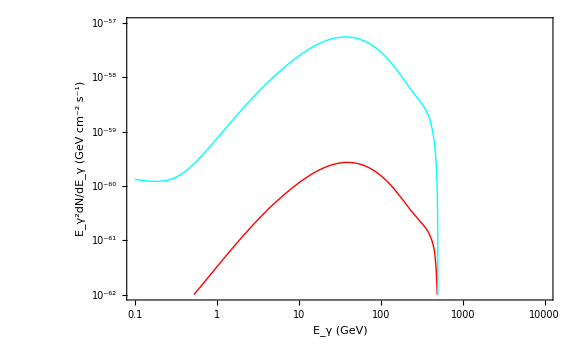

```mathematica
Show[pBDiffuseConstantBackground1000z23Redshift,pBDiffuseConstantBackground1000z46Redshift,
Axes->False,
Frame-> True,
FrameStyle-> Thickness[0.004],
FrameTicksStyle-> Thickness[0.004],
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
LabelStyle-> Directive[Bold,Black,FontFamily-> "Helvetica",FontSize-> 14],
ImageSize->Large
]
```

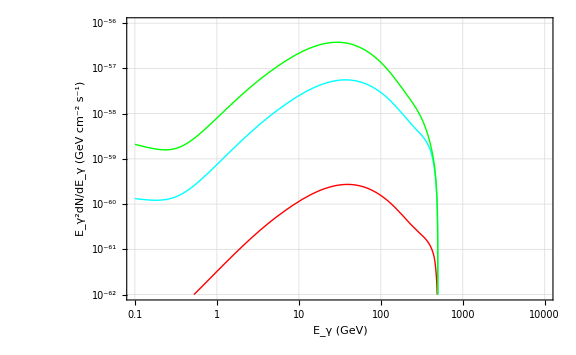

```mathematica
Module[{A,f1,f2,m1,envstyle,minE,maxE,expTicks},
A=2;
m1=81;
f1[x_]:=4/5. fVVqq[x]+1/5. fVVbb[x];
f2=fVVqq;
envstyle={(*Thick,*)Thickness[.01],Opacity[.3,Gray]};
minE=.75;
maxE=30;
expTicks=Table[{10^i,exponentForm[10^i]},{i,-8,-6}];
Show[pBDiffuseConstantBackground1000z23Redshift,pBDiffuseConstantBackground1000z46Redshift,pBDiffuseConstantBackground1000z100Redshift,PlotStyle->{
envstyle,
envstyle,
{Thickness[.008],Blue}
},
Filling->{1->{2}},
FillingStyle->{Opacity[.2,Yellow]},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
ImageSize->Large, (* or Large*)
Epilog->{
Text[Rotate[Style["m_χ→ bb",20,Gray],0Degree],ImageScaled@{.90,.25}],
Text[Rotate[Style["m_χ = 1 TeV",20,Gray],0Degree],ImageScaled@{.89,.15}]
(*Text[Rotate[Style["bb",19,Blue],0Degree],ImageScaled@{.27,.92}],
Text[Rotate[Style["m_χ=40 GeV",17,Blue],0Degree],ImageScaled@{.27,.78}],
Text[Rotate[Style["VV (V→qq)",19,Red],0Degree],ImageScaled@{.83,.84}],
Text[Rotate[Style["m_χ=81, m_V=21 GeV",17,Red],0Degree],ImageScaled@{.82,.76}],
Text[Rotate[Style["3φ (φ→bb)",19,Darker[Green]],0Degree],ImageScaled@{.5,.55}],
Text[Rotate[Style["m_χ=123, m_φ=27 GeV",17,Darker[Green]],0Degree],ImageScaled@{.5,.45}],
Text[Style["a=2",19,Gray],ImageScaled@{.2,.23}]*)
}
(*PlotLegends->Placed[LineLegend[Range[1,6],LegendLayout->{"Row",2}],{.35,.25}]*)
(*PlotTheme->"Detailed"*)
]]
```

### ----------------------------------------------------------------------------------------------------------------------------------------------------------------------- mDM = 10 TeV -----------------------------------------------------------------------------------------------------------------------------------------------------------------------

```mathematica
diffuseConstantBackgroundSpectrumBB10000z23 = GCascadeDiffuseConstant[injSpectrumBB10000,diffuseDistances[[23]],ρ];//AbsoluteTiming
```

Injected spectrum properly formatted

Successfully incorporated luminosity function. GCascade will produce spectra for diffuse background generated by your injected spectra.

{0.280172,Null}

```mathematica
diffuseDistances[[23]]
```

0.0005

```mathematica
diffuseConstantBackgroundSpectrumBB10000z46 = GCascadeDiffuseConstant[injSpectrumBB10000,diffuseDistances[[46]],ρ];//AbsoluteTiming
```

Injected spectrum properly formatted

Successfully incorporated luminosity function. GCascade will produce spectra for diffuse background generated by your injected spectra.

{45.1357,Null}

```mathematica
diffuseConstantBackgroundSpectrumBB10000z100 = GCascadeDiffuseConstant[injSpectrumBB10000,diffuseDistances[[100]],ρ];//AbsoluteTiming
```

Injected spectrum properly formatted

Successfully incorporated luminosity function. GCascade will produce spectra for diffuse background generated by your injected spectra.

{289.95,Null}

```mathematica
pBDiffuseConstantBackground10000z23 = LogLogPlot[Interpolation[Thread[{energies,energies^2 diffuseConstantBackgroundSpectrumBB10000z23}]][x],{x,10^-1,10^4},
PlotRange-> {{10^-1,10^4},{10^-61,10^-55}},
PlotStyle-> {Hue[1], Thick},
FrameTicks-> ticks
];
```

```mathematica
pBDiffuseConstantBackground10000z46 = LogLogPlot[Interpolation[Thread[{energies,energies^2 diffuseConstantBackgroundSpectrumBB10000z46}]][x],{x,10^-1,10^4},
PlotRange-> {{10^-1,10^4},{10^-61,10^-55}},
PlotStyle-> {Hue[1/2], Thick},
FrameTicks-> ticks
];
```

```mathematica
pBDiffuseConstantBackground10000z100 = LogLogPlot[Interpolation[Thread[{energies,energies^2 diffuseConstantBackgroundSpectrumBB10000z100}]][x],{x,10^-1,10^4},
PlotRange-> {{10^-1,10^4},{10^-61,10^-55}},
PlotStyle-> {Hue[1/3], Thick},
FrameTicks-> ticks
];
```

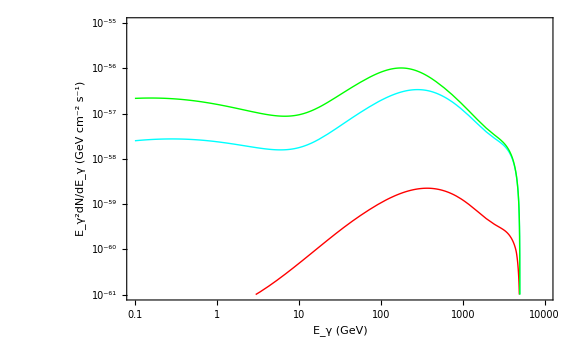

```mathematica
Show[pBDiffuseConstantBackground10000z23,pBDiffuseConstantBackground10000z46,pBDiffuseConstantBackground10000z100,
Axes->False,
Frame-> True,
FrameStyle-> Thickness[0.004],
FrameTicksStyle-> Thickness[0.004],
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
LabelStyle-> Directive[Bold,Black,FontFamily-> "Helvetica",FontSize-> 14],
ImageSize->Large
]
```

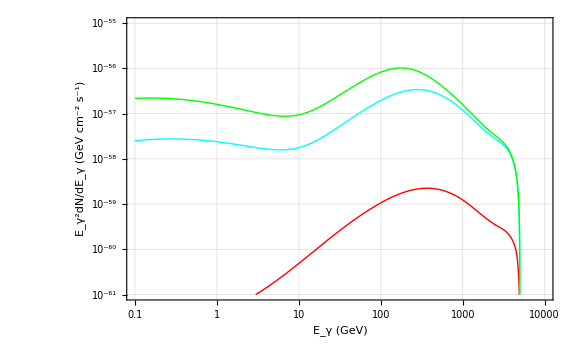

```mathematica
Module[{A,f1,f2,m1,envstyle,minE,maxE,expTicks},
A=2;
m1=81;
f1[x_]:=4/5. fVVqq[x]+1/5. fVVbb[x];
f2=fVVqq;
envstyle={(*Thick,*)Thickness[.01],Opacity[.3,Gray]};
minE=.75;
maxE=30;
expTicks=Table[{10^i,exponentForm[10^i]},{i,-8,-6}];
Show[pBDiffuseConstantBackground10000z23,pBDiffuseConstantBackground10000z46,pBDiffuseConstantBackground10000z100,PlotStyle->{
envstyle,
envstyle,
{Thickness[.008],Blue}
},
Filling->{1->{2}},
FillingStyle->{Opacity[.2,Yellow]},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
ImageSize->Large, (* or Large*)
Epilog->{
Text[Rotate[Style["m_χ→ bb",20,Gray],0Degree],ImageScaled@{.80,.25}],
Text[Rotate[Style["m_χ = 10 TeV",20,Gray],0Degree],ImageScaled@{.80,.15}]
(*Text[Rotate[Style["bb",19,Blue],0Degree],ImageScaled@{.27,.92}],
Text[Rotate[Style["m_χ=40 GeV",17,Blue],0Degree],ImageScaled@{.27,.78}],
Text[Rotate[Style["VV (V→qq)",19,Red],0Degree],ImageScaled@{.83,.84}],
Text[Rotate[Style["m_χ=81, m_V=21 GeV",17,Red],0Degree],ImageScaled@{.82,.76}],
Text[Rotate[Style["3φ (φ→bb)",19,Darker[Green]],0Degree],ImageScaled@{.5,.55}],
Text[Rotate[Style["m_χ=123, m_φ=27 GeV",17,Darker[Green]],0Degree],ImageScaled@{.5,.45}],
Text[Style["a=2",19,Gray],ImageScaled@{.2,.23}]*)
}
(*PlotLegends->Placed[LineLegend[Range[1,6],LegendLayout->{"Row",2}],{.35,.25}]*)
(*PlotTheme->"Detailed"*)
]]
```

#### With Redshift Dependence

```mathematica
diffuseConstantBackgroundSpectrumBB10000z23Redshift = GCascadeDiffuseConstant[injSpectrumBB10000,diffuseDistances[[23]],ρ2];//AbsoluteTiming
```

Injected spectrum properly formatted

Successfully incorporated luminosity function. GCascade will produce spectra for diffuse background generated by your injected spectra.

{0.279839,Null}

```mathematica
diffuseConstantBackgroundSpectrumBB10000z46Redshift = GCascadeDiffuseConstant[injSpectrumBB10000,diffuseDistances[[46]],ρ2];//AbsoluteTiming
```

Injected spectrum properly formatted

Successfully incorporated luminosity function. GCascade will produce spectra for diffuse background generated by your injected spectra.

{43.2568,Null}

```mathematica
diffuseConstantBackgroundSpectrumBB10000z100Redshift = GCascadeDiffuseConstant[injSpectrumBB10000,diffuseDistances[[100]],ρ2];//AbsoluteTiming
```

Injected spectrum properly formatted

Successfully incorporated luminosity function. GCascade will produce spectra for diffuse background generated by your injected spectra.

{286.617,Null}

```mathematica
pBDiffuseConstantBackground10000z23Redshift = LogLogPlot[Interpolation[Thread[{energies,energies^2 diffuseConstantBackgroundSpectrumBB10000z23Redshift}]][x],{x,10^-1,10^4},
PlotRange-> {{10^-1,10^4},{10^-61,10^-55}},
PlotStyle-> {Hue[1], Thick},
FrameTicks-> ticks
];
```

```mathematica
pBDiffuseConstantBackground10000z46Redshift = LogLogPlot[Interpolation[Thread[{energies,energies^2 diffuseConstantBackgroundSpectrumBB10000z46Redshift}]][x],{x,10^-1,10^4},
PlotRange-> {{10^-1,10^4},{10^-61,10^-55}},
PlotStyle-> {Hue[1/2], Thick},
FrameTicks-> ticks
];
```

```mathematica
pBDiffuseConstantBackground10000z100Redshift = LogLogPlot[Interpolation[Thread[{energies,energies^2 diffuseConstantBackgroundSpectrumBB10000z100Redshift}]][x],{x,10^-1,10^4},
PlotRange-> {{10^-1,10^4},{10^-61,10^-55}},
PlotStyle-> {Hue[1/3], Thick},
FrameTicks-> ticks
];
```

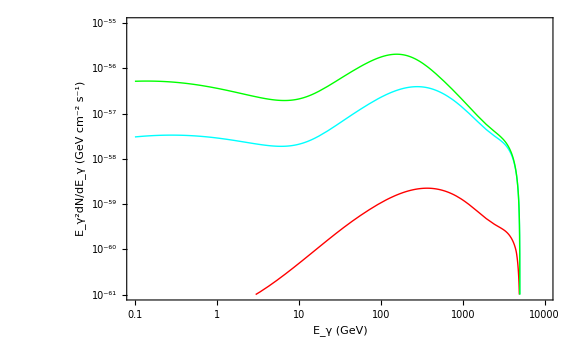

```mathematica
Show[pBDiffuseConstantBackground10000z23Redshift,pBDiffuseConstantBackground10000z46Redshift,pBDiffuseConstantBackground10000z100Redshift,
Axes->False,
Frame-> True,
FrameStyle-> Thickness[0.004],
FrameTicksStyle-> Thickness[0.004],
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
LabelStyle-> Directive[Bold,Black,FontFamily-> "Helvetica",FontSize-> 14],
ImageSize->Large
]
```

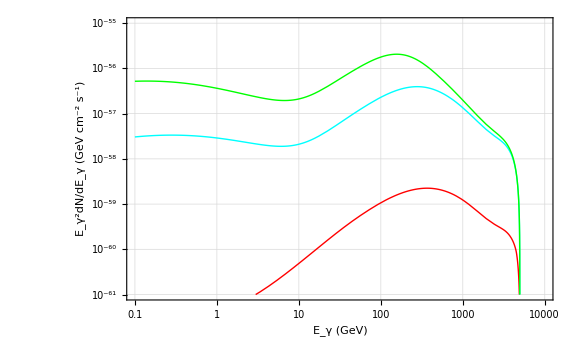

```mathematica
Module[{A,f1,f2,m1,envstyle,minE,maxE,expTicks},
A=2;
m1=81;
f1[x_]:=4/5. fVVqq[x]+1/5. fVVbb[x];
f2=fVVqq;
envstyle={(*Thick,*)Thickness[.01],Opacity[.3,Gray]};
minE=.75;
maxE=30;
expTicks=Table[{10^i,exponentForm[10^i]},{i,-8,-6}];
Show[pBDiffuseConstantBackground10000z23Redshift,pBDiffuseConstantBackground10000z46Redshift,pBDiffuseConstantBackground10000z100Redshift,PlotStyle->{
envstyle,
envstyle,
{Thickness[.008],Blue}
},
Filling->{1->{2}},
FillingStyle->{Opacity[.2,Yellow]},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
ImageSize->Large, (* or Large*)
Epilog->{
Text[Rotate[Style["m_χ→ bb",20,Gray],0Degree],ImageScaled@{.80,.25}],
Text[Rotate[Style["m_χ = 10 TeV",20,Gray],0Degree],ImageScaled@{.80,.15}]
(*Text[Rotate[Style["bb",19,Blue],0Degree],ImageScaled@{.27,.92}],
Text[Rotate[Style["m_χ=40 GeV",17,Blue],0Degree],ImageScaled@{.27,.78}],
Text[Rotate[Style["VV (V→qq)",19,Red],0Degree],ImageScaled@{.83,.84}],
Text[Rotate[Style["m_χ=81, m_V=21 GeV",17,Red],0Degree],ImageScaled@{.82,.76}],
Text[Rotate[Style["3φ (φ→bb)",19,Darker[Green]],0Degree],ImageScaled@{.5,.55}],
Text[Rotate[Style["m_χ=123, m_φ=27 GeV",17,Darker[Green]],0Degree],ImageScaled@{.5,.45}],
Text[Style["a=2",19,Gray],ImageScaled@{.2,.23}]*)
}
(*PlotLegends->Placed[LineLegend[Range[1,6],LegendLayout->{"Row",2}],{.35,.25}]*)
(*PlotTheme->"Detailed"*)
]]
```

### ----------------------------------------------------------------------------------------------------------------------------------------------------------------------- mDM = 100 TeV -----------------------------------------------------------------------------------------------------------------------------------------------------------------------

```mathematica
diffuseConstantBackgroundSpectrumBB100000z23 = GCascadeDiffuseConstant[injSpectrumBB100000,diffuseDistances[[23]],ρ];//AbsoluteTiming
```

Injected spectrum properly formatted

Successfully incorporated luminosity function. GCascade will produce spectra for diffuse background generated by your injected spectra.

{0.299572,Null}

```mathematica
diffuseDistances[[23]]
```

0.0005

```mathematica
diffuseConstantBackgroundSpectrumBB100000z46 = GCascadeDiffuseConstant[injSpectrumBB100000,diffuseDistances[[46]],ρ];//AbsoluteTiming
```

Injected spectrum properly formatted

Successfully incorporated luminosity function. GCascade will produce spectra for diffuse background generated by your injected spectra.

{40.8123,Null}

```mathematica
diffuseConstantBackgroundSpectrumBB100000z100 = GCascadeDiffuseConstant[injSpectrumBB100000,diffuseDistances[[100]],ρ];//AbsoluteTiming
```

Injected spectrum properly formatted

Successfully incorporated luminosity function. GCascade will produce spectra for diffuse background generated by your injected spectra.

{281.634,Null}

```mathematica
pBDiffuseConstantBackground100000z23 = LogLogPlot[Interpolation[Thread[{energies,energies^2 diffuseConstantBackgroundSpectrumBB100000z23}]][x],{x,10^-1,10^5},
PlotRange-> {{10^-1,10^5},{10^-61,10^-55}},
PlotStyle-> {Hue[1], Thick},
FrameTicks-> ticks
];
```

```mathematica
pBDiffuseConstantBackground100000z46 = LogLogPlot[Interpolation[Thread[{energies,energies^2 diffuseConstantBackgroundSpectrumBB100000z46}]][x],{x,10^-1,10^5},
PlotRange-> {{10^-1,10^5},{10^-61,10^-55}},
PlotStyle-> {Hue[1/2], Thick},
FrameTicks-> ticks
];
```

```mathematica
pBDiffuseConstantBackground100000z100 = LogLogPlot[Interpolation[Thread[{energies,energies^2 diffuseConstantBackgroundSpectrumBB100000z100}]][x],{x,10^-1,10^5},
PlotRange-> {{10^-1,10^5},{10^-61,10^-55}},
PlotStyle-> {Hue[1/3], Thick},
FrameTicks-> ticks
];
```

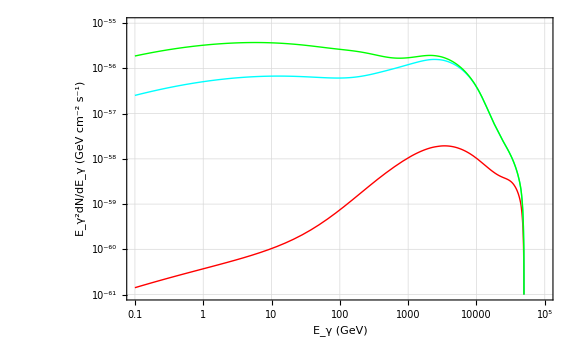

```mathematica
Module[{A,f1,f2,m1,envstyle,minE,maxE,expTicks},
A=2;
m1=81;
f1[x_]:=4/5. fVVqq[x]+1/5. fVVbb[x];
f2=fVVqq;
envstyle={(*Thick,*)Thickness[.01],Opacity[.3,Gray]};
minE=.75;
maxE=30;
expTicks=Table[{10^i,exponentForm[10^i]},{i,-8,-6}];
Show[pBDiffuseConstantBackground100000z23,pBDiffuseConstantBackground100000z46,pBDiffuseConstantBackground100000z100,PlotStyle->{
envstyle,
envstyle,
{Thickness[.008],Blue}
},
Filling->{1->{2}},
FillingStyle->{Opacity[.2,Yellow]},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
ImageSize->Large, (* or Large*)
Epilog->{
Text[Rotate[Style["m_χ→ bb",20,Gray],0Degree],ImageScaled@{.80,.25}],
Text[Rotate[Style["m_χ = 100 TeV",20,Gray],0Degree],ImageScaled@{.80,.15}]
(*Text[Rotate[Style["bb",19,Blue],0Degree],ImageScaled@{.27,.92}],
Text[Rotate[Style["m_χ=40 GeV",17,Blue],0Degree],ImageScaled@{.27,.78}],
Text[Rotate[Style["VV (V→qq)",19,Red],0Degree],ImageScaled@{.83,.84}],
Text[Rotate[Style["m_χ=81, m_V=21 GeV",17,Red],0Degree],ImageScaled@{.82,.76}],
Text[Rotate[Style["3φ (φ→bb)",19,Darker[Green]],0Degree],ImageScaled@{.5,.55}],
Text[Rotate[Style["m_χ=123, m_φ=27 GeV",17,Darker[Green]],0Degree],ImageScaled@{.5,.45}],
Text[Style["a=2",19,Gray],ImageScaled@{.2,.23}]*)
}
(*PlotLegends->Placed[LineLegend[Range[1,6],LegendLayout->{"Row",2}],{.35,.25}]*)
(*PlotTheme->"Detailed"*)
]]
```

```mathematica
Export["/Users/barbaraskrzypek/Documents/IceCube/GCascade-master/diffuseConstantBackgroundBB100000.jpeg",%]
```

/Users/barbaraskrzypek/Documents/IceCube/GCascade-master/diffuseConstantBackgroundBB100000.jpeg

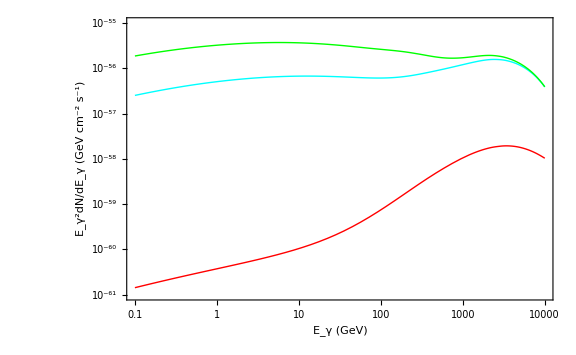

```mathematica
Show[pBDiffuseConstantBackground100000z23,pBDiffuseConstantBackground100000z46,pBDiffuseConstantBackground100000z100,
Axes->False,
Frame-> True,
FrameStyle-> Thickness[0.004],
FrameTicksStyle-> Thickness[0.004],
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
LabelStyle-> Directive[Bold,Black,FontFamily-> "Helvetica",FontSize-> 14],
ImageSize->Large
]
```

#### With Redshift Dependence

```mathematica
diffuseConstantBackgroundSpectrumBB100000z23Redshift = GCascadeDiffuseConstant[injSpectrumBB100000,diffuseDistances[[23]],ρ2];//AbsoluteTiming
```

Injected spectrum properly formatted

Successfully incorporated luminosity function. GCascade will produce spectra for diffuse background generated by your injected spectra.

{0.296348,Null}

```mathematica
diffuseConstantBackgroundSpectrumBB100000z46Redshift = GCascadeDiffuseConstant[injSpectrumBB100000,diffuseDistances[[46]],ρ2];//AbsoluteTiming
```

Injected spectrum properly formatted

Successfully incorporated luminosity function. GCascade will produce spectra for diffuse background generated by your injected spectra.

{43.0152,Null}

```mathematica
diffuseConstantBackgroundSpectrumBB100000z100Redshift = GCascadeDiffuseConstant[injSpectrumBB100000,diffuseDistances[[100]],ρ2];//AbsoluteTiming
```

Injected spectrum properly formatted

Successfully incorporated luminosity function. GCascade will produce spectra for diffuse background generated by your injected spectra.

{286.578,Null}

```mathematica
pBDiffuseConstantBackground100000z23Redshift = LogLogPlot[Interpolation[Thread[{energies,energies^2 diffuseConstantBackgroundSpectrumBB100000z23Redshift}]][x],{x,10^-1,10^4},
PlotRange-> {{10^-1,10^4},{10^-61,10^-55}},
PlotStyle-> {Hue[1], Thick},
FrameTicks-> ticks
];
```

```mathematica
pBDiffuseConstantBackground100000z46Redshift = LogLogPlot[Interpolation[Thread[{energies,energies^2 diffuseConstantBackgroundSpectrumBB100000z46Redshift}]][x],{x,10^-1,10^4},
PlotRange-> {{10^-1,10^4},{10^-61,10^-55}},
PlotStyle-> {Hue[1/2], Thick},
FrameTicks-> ticks
];
```

```mathematica
pBDiffuseConstantBackground100000z100Redshift = LogLogPlot[Interpolation[Thread[{energies,energies^2 diffuseConstantBackgroundSpectrumBB100000z100Redshift}]][x],{x,10^-1,10^4},
PlotRange-> {{10^-1,10^4},{10^-61,10^-55}},
PlotStyle-> {Hue[1/3], Thick},
FrameTicks-> ticks
];
```

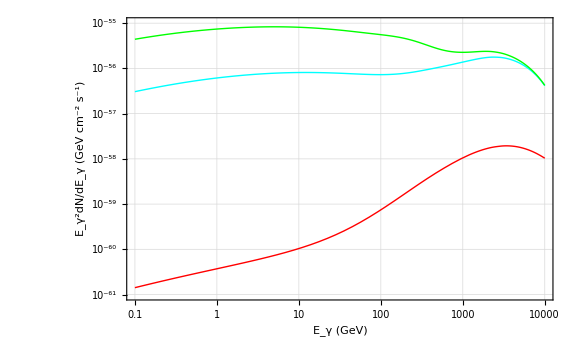

```mathematica
Module[{A,f1,f2,m1,envstyle,minE,maxE,expTicks},
A=2;
m1=81;
f1[x_]:=4/5. fVVqq[x]+1/5. fVVbb[x];
f2=fVVqq;
envstyle={(*Thick,*)Thickness[.01],Opacity[.3,Gray]};
minE=.75;
maxE=30;
expTicks=Table[{10^i,exponentForm[10^i]},{i,-8,-6}];
Show[pBDiffuseConstantBackground100000z23Redshift,pBDiffuseConstantBackground100000z46Redshift,pBDiffuseConstantBackground100000z100Redshift,PlotStyle->{
envstyle,
envstyle,
{Thickness[.008],Blue}
},
Filling->{1->{2}},
FillingStyle->{Opacity[.2,Yellow]},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
ImageSize->Large, (* or Large*)
Epilog->{
Text[Rotate[Style["m_χ→ bb",20,Gray],0Degree],ImageScaled@{.80,.25}],
Text[Rotate[Style["m_χ = 100 TeV",20,Gray],0Degree],ImageScaled@{.80,.15}]
(*Text[Rotate[Style["bb",19,Blue],0Degree],ImageScaled@{.27,.92}],
Text[Rotate[Style["m_χ=40 GeV",17,Blue],0Degree],ImageScaled@{.27,.78}],
Text[Rotate[Style["VV (V→qq)",19,Red],0Degree],ImageScaled@{.83,.84}],
Text[Rotate[Style["m_χ=81, m_V=21 GeV",17,Red],0Degree],ImageScaled@{.82,.76}],
Text[Rotate[Style["3φ (φ→bb)",19,Darker[Green]],0Degree],ImageScaled@{.5,.55}],
Text[Rotate[Style["m_χ=123, m_φ=27 GeV",17,Darker[Green]],0Degree],ImageScaled@{.5,.45}],
Text[Style["a=2",19,Gray],ImageScaled@{.2,.23}]*)
}
(*PlotLegends->Placed[LineLegend[Range[1,6],LegendLayout->{"Row",2}],{.35,.25}]*)
(*PlotTheme->"Detailed"*)
]]
```

## WW Decay Mode

### ----------------------------------------------------------------------------------------------------------------------------------------------------------------------- mDM = 1 TeV -----------------------------------------------------------------------------------------------------------------------------------------------------------------------

```mathematica
diffuseConstantBackgroundSpectrumWW1000z23 = GCascadeDiffuseConstant[injSpectrumWW1000,diffuseDistances[[23]],ρ];//AbsoluteTiming
```

{2.56282,Null}

Successfully incorporated luminosity function. GCascade will produce spectra for diffuse background generated by your injected spectra.

Injected spectrum properly formatted

Injected spectrum properly formatted

Successfully incorporated luminosity function. GCascade will produce spectra for diffuse background generated by your injected spectra.

{0.280172,Null}

```mathematica
diffuseDistances[[23]]
```

0.0005

```mathematica
diffuseConstantBackgroundSpectrumBBWW1000z46 = GCascadeDiffuseConstant[injSpectrumWW1000,diffuseDistances[[46]],ρ];//AbsoluteTiming
```

Injected spectrum properly formatted

Successfully incorporated luminosity function. GCascade will produce spectra for diffuse background generated by your injected spectra.

{278.836,Null}

```mathematica
diffuseConstantBackgroundSpectrumBB10000z100 = GCascadeDiffuseConstant[injSpectrumBB10000,diffuseDistances[[100]],ρ];//AbsoluteTiming
```

Injected spectrum properly formatted

Successfully incorporated luminosity function. GCascade will produce spectra for diffuse background generated by your injected spectra.

{289.95,Null}

```mathematica
pBDiffuseConstantBackground10000z23 = LogLogPlot[Interpolation[Thread[{energies,energies^2 diffuseConstantBackgroundSpectrumBB10000z23}]][x],{x,10^-1,10^4},
PlotRange-> {{10^-1,10^4},{10^-61,10^-55}},
PlotStyle-> {Hue[1], Thick},
FrameTicks-> ticks
];
```

```mathematica
pBDiffuseConstantBackground10000z46 = LogLogPlot[Interpolation[Thread[{energies,energies^2 diffuseConstantBackgroundSpectrumBB10000z46}]][x],{x,10^-1,10^4},
PlotRange-> {{10^-1,10^4},{10^-61,10^-55}},
PlotStyle-> {Hue[1/2], Thick},
FrameTicks-> ticks
];
```

```mathematica
pBDiffuseConstantBackground10000z100 = LogLogPlot[Interpolation[Thread[{energies,energies^2 diffuseConstantBackgroundSpectrumBB10000z100}]][x],{x,10^-1,10^4},
PlotRange-> {{10^-1,10^4},{10^-61,10^-55}},
PlotStyle-> {Hue[1/3], Thick},
FrameTicks-> ticks
];
```

```mathematica
Show[pBDiffuseConstantBackground10000z23,pBDiffuseConstantBackground10000z46,pBDiffuseConstantBackground10000z100,
Axes->False,
Frame-> True,
FrameStyle-> Thickness[0.004],
FrameTicksStyle-> Thickness[0.004],
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
LabelStyle-> Directive[Bold,Black,FontFamily-> "Helvetica",FontSize-> 14],
ImageSize->Large
]
```

-Graphics-

#### With Redshift Dependence

```mathematica
diffuseConstantBackgroundSpectrumWW1000z23Redshift = GCascadeDiffuseConstant[injSpectrumWW1000,diffuseDistances[[23]],ρ2];//AbsoluteTiming
```

Injected spectrum properly formatted

Successfully incorporated luminosity function. GCascade will produce spectra for diffuse background generated by your injected spectra.

{2.56328,Null}

```mathematica
diffuseConstantBackgroundSpectrumWW1000z46Redshift = GCascadeDiffuseConstant[injSpectrumWW1000,diffuseDistances[[46]],ρ2];//AbsoluteTiming
```

Injected spectrum properly formatted

Successfully incorporated luminosity function. GCascade will produce spectra for diffuse background generated by your injected spectra.

{401.337,Null}

```mathematica
diffuseConstantBackgroundSpectrumWW1000z100Redshift = GCascadeDiffuseConstant[injSpectrumWW1000,diffuseDistances[[100]],ρ2];//AbsoluteTiming
```

Injected spectrum properly formatted

Successfully incorporated luminosity function. GCascade will produce spectra for diffuse background generated by your injected spectra.

{1774.28,Null}

```mathematica
pWDiffuseConstantBackground1000z23Redshift = LogLogPlot[Interpolation[Thread[{energies,energies^2 diffuseConstantBackgroundSpectrumWW1000z23Redshift}]][x],{x,10^-1,10^4},
PlotRange-> {{10^-1,10^4},{10^-61,10^-55}},
PlotStyle-> {Hue[1], Thick},
FrameTicks-> ticks
];
```

```mathematica
pWDiffuseConstantBackground1000z46Redshift = LogLogPlot[Interpolation[Thread[{energies,energies^2 diffuseConstantBackgroundSpectrumWW1000z46Redshift}]][x],{x,10^-1,10^4},
PlotRange-> {{10^-1,10^4},{10^-61,10^-55}},
PlotStyle-> {Hue[1/2], Thick},
FrameTicks-> ticks
];
```

```mathematica
pWDiffuseConstantBackground1000z100Redshift = LogLogPlot[Interpolation[Thread[{energies,energies^2 diffuseConstantBackgroundSpectrumWW1000z100Redshift}]][x],{x,10^-1,10^4},
PlotRange-> {{10^-1,10^4},{10^-61,10^-55}},
PlotStyle-> {Hue[1/3], Thick},
FrameTicks-> ticks
];
```

```mathematica
Show[pBDiffuseConstantBackground10000z23Redshift,pBDiffuseConstantBackground10000z46Redshift,pBDiffuseConstantBackground10000z100Redshift,
Axes->False,
Frame-> True,
FrameStyle-> Thickness[0.004],
FrameTicksStyle-> Thickness[0.004],
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
LabelStyle-> Directive[Bold,Black,FontFamily-> "Helvetica",FontSize-> 14],
ImageSize->Large
]
```

-Graphics-

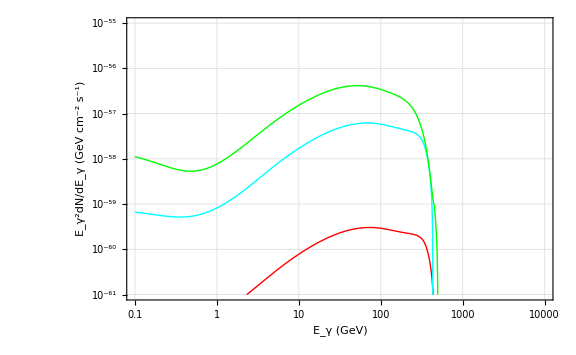

```mathematica
Module[{A,f1,f2,m1,envstyle,minE,maxE,expTicks},
A=2;
m1=81;
f1[x_]:=4/5. fVVqq[x]+1/5. fVVbb[x];
f2=fVVqq;
envstyle={(*Thick,*)Thickness[.01],Opacity[.3,Gray]};
minE=.75;
maxE=30;
expTicks=Table[{10^i,exponentForm[10^i]},{i,-8,-6}];
Show[pWDiffuseConstantBackground1000z23Redshift,pWDiffuseConstantBackground1000z46Redshift,pWDiffuseConstantBackground1000z100Redshift,PlotStyle->{
envstyle,
envstyle,
{Thickness[.008],Blue}
},
Filling->{1->{2}},
FillingStyle->{Opacity[.2,Yellow]},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
ImageSize->Large, (* or Large*)
Epilog->{
Text[Rotate[Style["m_χ→ WW",20,Gray],0Degree],ImageScaled@{.87,.25}],
Text[Rotate[Style["m_χ = 1 TeV",20,Gray],0Degree],ImageScaled@{.86,.15}]
(*Text[Rotate[Style["bb",19,Blue],0Degree],ImageScaled@{.27,.92}],
Text[Rotate[Style["m_χ=40 GeV",17,Blue],0Degree],ImageScaled@{.27,.78}],
Text[Rotate[Style["VV (V→qq)",19,Red],0Degree],ImageScaled@{.83,.84}],
Text[Rotate[Style["m_χ=81, m_V=21 GeV",17,Red],0Degree],ImageScaled@{.82,.76}],
Text[Rotate[Style["3φ (φ→bb)",19,Darker[Green]],0Degree],ImageScaled@{.5,.55}],
Text[Rotate[Style["m_χ=123, m_φ=27 GeV",17,Darker[Green]],0Degree],ImageScaled@{.5,.45}],
Text[Style["a=2",19,Gray],ImageScaled@{.2,.23}]*)
}
(*PlotLegends->Placed[LineLegend[Range[1,6],LegendLayout->{"Row",2}],{.35,.25}]*)
(*PlotTheme->"Detailed"*)
]]
```

### ----------------------------------------------------------------------------------------------------------------------------------------------------------------------- mDM = 10 TeV -----------------------------------------------------------------------------------------------------------------------------------------------------------------------

```mathematica
diffuseConstantBackgroundSpectrumWW10000z23 = GCascadeDiffuseConstant[injSpectrumWW10000,diffuseDistances[[23]],ρ];//AbsoluteTiming
```

Injected spectrum properly formatted

Successfully incorporated luminosity function. GCascade will produce spectra for diffuse background generated by your injected spectra.

{0.305393,Null}

Successfully incorporated luminosity function. GCascade will produce spectra for diffuse background generated by your injected spectra.

Injected spectrum properly formatted

Injected spectrum properly formatted

Successfully incorporated luminosity function. GCascade will produce spectra for diffuse background generated by your injected spectra.

{0.280172,Null}

```mathematica
diffuseDistances[[23]]
```

0.0005

```mathematica
diffuseConstantBackgroundSpectrumBBWW10000z46 = GCascadeDiffuseConstant[injSpectrumWW10000,diffuseDistances[[46]],ρ];//AbsoluteTiming
```

Injected spectrum properly formatted

Successfully incorporated luminosity function. GCascade will produce spectra for diffuse background generated by your injected spectra.

$Aborted

```mathematica
diffuseConstantBackgroundSpectrumBB10000z100 = GCascadeDiffuseConstant[injSpectrumBB10000,diffuseDistances[[100]],ρ];//AbsoluteTiming
```

Injected spectrum properly formatted

Successfully incorporated luminosity function. GCascade will produce spectra for diffuse background generated by your injected spectra.

{289.95,Null}

```mathematica
pBDiffuseConstantBackground10000z23 = LogLogPlot[Interpolation[Thread[{energies,energies^2 diffuseConstantBackgroundSpectrumBB10000z23}]][x],{x,10^-1,10^4},
PlotRange-> {{10^-1,10^4},{10^-61,10^-55}},
PlotStyle-> {Hue[1], Thick},
FrameTicks-> ticks
];
```

```mathematica
pBDiffuseConstantBackground10000z46 = LogLogPlot[Interpolation[Thread[{energies,energies^2 diffuseConstantBackgroundSpectrumBB10000z46}]][x],{x,10^-1,10^4},
PlotRange-> {{10^-1,10^4},{10^-61,10^-55}},
PlotStyle-> {Hue[1/2], Thick},
FrameTicks-> ticks
];
```

```mathematica
pBDiffuseConstantBackground10000z100 = LogLogPlot[Interpolation[Thread[{energies,energies^2 diffuseConstantBackgroundSpectrumBB10000z100}]][x],{x,10^-1,10^4},
PlotRange-> {{10^-1,10^4},{10^-61,10^-55}},
PlotStyle-> {Hue[1/3], Thick},
FrameTicks-> ticks
];
```

```mathematica
Show[pBDiffuseConstantBackground10000z23,pBDiffuseConstantBackground10000z46,pBDiffuseConstantBackground10000z100,
Axes->False,
Frame-> True,
FrameStyle-> Thickness[0.004],
FrameTicksStyle-> Thickness[0.004],
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
LabelStyle-> Directive[Bold,Black,FontFamily-> "Helvetica",FontSize-> 14],
ImageSize->Large
]
```

-Graphics-

#### With Redshift Dependence

```mathematica
diffuseConstantBackgroundSpectrumWW10000z23Redshift = GCascadeDiffuseConstant[injSpectrumWW10000,diffuseDistances[[23]],ρ2];//AbsoluteTiming
```

Injected spectrum properly formatted

Successfully incorporated luminosity function. GCascade will produce spectra for diffuse background generated by your injected spectra.

{0.272473,Null}

```mathematica
diffuseConstantBackgroundSpectrumWW10000z46Redshift = GCascadeDiffuseConstant[injSpectrumWW10000,diffuseDistances[[46]],ρ2];//AbsoluteTiming
```

Injected spectrum properly formatted

Successfully incorporated luminosity function. GCascade will produce spectra for diffuse background generated by your injected spectra.

{45.9458,Null}

```mathematica
diffuseConstantBackgroundSpectrumWW1000z100Redshift = GCascadeDiffuseConstant[injSpectrumWW1000,diffuseDistances[[100]],ρ2];//AbsoluteTiming
```

Injected spectrum properly formatted

Successfully incorporated luminosity function. GCascade will produce spectra for diffuse background generated by your injected spectra.

{1774.28,Null}

```mathematica
pWDiffuseConstantBackground10000z23Redshift = LogLogPlot[Interpolation[Thread[{energies,energies^2 diffuseConstantBackgroundSpectrumWW10000z23Redshift}]][x],{x,10^-1,10^4},
PlotRange-> {{10^-1,10^4},{10^-61,10^-55}},
PlotStyle-> {Hue[1], Thick},
FrameTicks-> ticks
];
```

```mathematica
pWDiffuseConstantBackground10000z46Redshift = LogLogPlot[Interpolation[Thread[{energies,energies^2 diffuseConstantBackgroundSpectrumWW10000z46Redshift}]][x],{x,10^-1,10^4},
PlotRange-> {{10^-1,10^4},{10^-61,10^-55}},
PlotStyle-> {Hue[1/2], Thick},
FrameTicks-> ticks
];
```

```mathematica
pWDiffuseConstantBackground1000z100Redshift = LogLogPlot[Interpolation[Thread[{energies,energies^2 diffuseConstantBackgroundSpectrumWW1000z100Redshift}]][x],{x,10^-1,10^4},
PlotRange-> {{10^-1,10^4},{10^-61,10^-55}},
PlotStyle-> {Hue[1/3], Thick},
FrameTicks-> ticks
];
```

```mathematica
Show[pBDiffuseConstantBackground10000z23Redshift,pBDiffuseConstantBackground10000z46Redshift,pBDiffuseConstantBackground10000z100Redshift,
Axes->False,
Frame-> True,
FrameStyle-> Thickness[0.004],
FrameTicksStyle-> Thickness[0.004],
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
LabelStyle-> Directive[Bold,Black,FontFamily-> "Helvetica",FontSize-> 14],
ImageSize->Large
]
```

-Graphics-

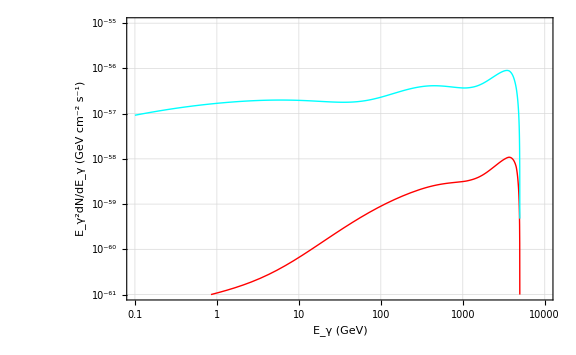

```mathematica
Module[{A,f1,f2,m1,envstyle,minE,maxE,expTicks},
A=2;
m1=81;
f1[x_]:=4/5. fVVqq[x]+1/5. fVVbb[x];
f2=fVVqq;
envstyle={(*Thick,*)Thickness[.01],Opacity[.3,Gray]};
minE=.75;
maxE=30;
expTicks=Table[{10^i,exponentForm[10^i]},{i,-8,-6}];
Show[pWDiffuseConstantBackground10000z23Redshift,pWDiffuseConstantBackground10000z46Redshift,
PlotStyle->{
envstyle,
envstyle,
{Thickness[.008],Blue}
},
Filling->{1->{2}},
FillingStyle->{Opacity[.2,Yellow]},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
ImageSize->Large, (* or Large*)
Epilog->{
Text[Rotate[Style["m_χ→ WW",20,Gray],0Degree],ImageScaled@{.75,.25}],
Text[Rotate[Style["m_χ = 10 TeV",20,Gray],0Degree],ImageScaled@{.75,.15}]
(*Text[Rotate[Style["bb",19,Blue],0Degree],ImageScaled@{.27,.92}],
Text[Rotate[Style["m_χ=40 GeV",17,Blue],0Degree],ImageScaled@{.27,.78}],
Text[Rotate[Style["VV (V→qq)",19,Red],0Degree],ImageScaled@{.83,.84}],
Text[Rotate[Style["m_χ=81, m_V=21 GeV",17,Red],0Degree],ImageScaled@{.82,.76}],
Text[Rotate[Style["3φ (φ→bb)",19,Darker[Green]],0Degree],ImageScaled@{.5,.55}],
Text[Rotate[Style["m_χ=123, m_φ=27 GeV",17,Darker[Green]],0Degree],ImageScaled@{.5,.45}],
Text[Style["a=2",19,Gray],ImageScaled@{.2,.23}]*)
}
(*PlotLegends->Placed[LineLegend[Range[1,6],LegendLayout->{"Row",2}],{.35,.25}]*)
(*PlotTheme->"Detailed"*)
]]
```

### ----------------------------------------------------------------------------------------------------------------------------------------------------------------------- mDM = 100 TeV -----------------------------------------------------------------------------------------------------------------------------------------------------------------------

```mathematica
diffuseConstantBackgroundSpectrumWW10000z23 = GCascadeDiffuseConstant[injSpectrumWW10000,diffuseDistances[[23]],ρ];//AbsoluteTiming
```

Injected spectrum properly formatted

Successfully incorporated luminosity function. GCascade will produce spectra for diffuse background generated by your injected spectra.

{0.305393,Null}

Successfully incorporated luminosity function. GCascade will produce spectra for diffuse background generated by your injected spectra.

Injected spectrum properly formatted

Injected spectrum properly formatted

Successfully incorporated luminosity function. GCascade will produce spectra for diffuse background generated by your injected spectra.

{0.280172,Null}

```mathematica
diffuseDistances[[23]]
```

0.0005

```mathematica
diffuseConstantBackgroundSpectrumBBWW10000z46 = GCascadeDiffuseConstant[injSpectrumWW10000,diffuseDistances[[46]],ρ];//AbsoluteTiming
```

Injected spectrum properly formatted

Successfully incorporated luminosity function. GCascade will produce spectra for diffuse background generated by your injected spectra.

$Aborted

```mathematica
diffuseConstantBackgroundSpectrumBB10000z100 = GCascadeDiffuseConstant[injSpectrumBB10000,diffuseDistances[[100]],ρ];//AbsoluteTiming
```

Injected spectrum properly formatted

Successfully incorporated luminosity function. GCascade will produce spectra for diffuse background generated by your injected spectra.

{289.95,Null}

```mathematica
pBDiffuseConstantBackground10000z23 = LogLogPlot[Interpolation[Thread[{energies,energies^2 diffuseConstantBackgroundSpectrumBB10000z23}]][x],{x,10^-1,10^4},
PlotRange-> {{10^-1,10^4},{10^-61,10^-55}},
PlotStyle-> {Hue[1], Thick},
FrameTicks-> ticks
];
```

```mathematica
pBDiffuseConstantBackground10000z46 = LogLogPlot[Interpolation[Thread[{energies,energies^2 diffuseConstantBackgroundSpectrumBB10000z46}]][x],{x,10^-1,10^4},
PlotRange-> {{10^-1,10^4},{10^-61,10^-55}},
PlotStyle-> {Hue[1/2], Thick},
FrameTicks-> ticks
];
```

```mathematica
pBDiffuseConstantBackground10000z100 = LogLogPlot[Interpolation[Thread[{energies,energies^2 diffuseConstantBackgroundSpectrumBB10000z100}]][x],{x,10^-1,10^4},
PlotRange-> {{10^-1,10^4},{10^-61,10^-55}},
PlotStyle-> {Hue[1/3], Thick},
FrameTicks-> ticks
];
```

```mathematica
Show[pBDiffuseConstantBackground10000z23,pBDiffuseConstantBackground10000z46,pBDiffuseConstantBackground10000z100,
Axes->False,
Frame-> True,
FrameStyle-> Thickness[0.004],
FrameTicksStyle-> Thickness[0.004],
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
LabelStyle-> Directive[Bold,Black,FontFamily-> "Helvetica",FontSize-> 14],
ImageSize->Large
]
```

-Graphics-

#### With Redshift Dependence

```mathematica
diffuseConstantBackgroundSpectrumWW100000z23Redshift = GCascadeDiffuseConstant[injSpectrumWW100000,diffuseDistances[[23]],ρ2];//AbsoluteTiming
```

Injected spectrum properly formatted

Successfully incorporated luminosity function. GCascade will produce spectra for diffuse background generated by your injected spectra.

{0.298199,Null}

```mathematica
diffuseConstantBackgroundSpectrumWW100000z46Redshift = GCascadeDiffuseConstant[injSpectrumWW100000,diffuseDistances[[46]],ρ2];//AbsoluteTiming
```

Injected spectrum properly formatted

Successfully incorporated luminosity function. GCascade will produce spectra for diffuse background generated by your injected spectra.

{47.2514,Null}

```mathematica
diffuseConstantBackgroundSpectrumWW1000z100Redshift = GCascadeDiffuseConstant[injSpectrumWW1000,diffuseDistances[[100]],ρ2];//AbsoluteTiming
```

Injected spectrum properly formatted

Successfully incorporated luminosity function. GCascade will produce spectra for diffuse background generated by your injected spectra.

{1774.28,Null}

```mathematica
pWDiffuseConstantBackground100000z23Redshift = LogLogPlot[Interpolation[Thread[{energies,energies^2 diffuseConstantBackgroundSpectrumWW100000z23Redshift}]][x],{x,10^-1,10^6},
PlotRange-> {{10^-1,10^6},{10^-61,10^-55}},
PlotStyle-> {Hue[1], Thick},
FrameTicks-> ticks
];
```

```mathematica
pWDiffuseConstantBackground100000z46Redshift = LogLogPlot[Interpolation[Thread[{energies,energies^2 diffuseConstantBackgroundSpectrumWW100000z46Redshift}]][x],{x,10^-1,10^6},
PlotRange-> {{10^-1,10^6},{10^-61,10^-55}},
PlotStyle-> {Hue[1/2], Thick},
FrameTicks-> ticks
];
```

```mathematica
pWDiffuseConstantBackground1000z100Redshift = LogLogPlot[Interpolation[Thread[{energies,energies^2 diffuseConstantBackgroundSpectrumWW1000z100Redshift}]][x],{x,10^-1,10^4},
PlotRange-> {{10^-1,10^4},{10^-61,10^-55}},
PlotStyle-> {Hue[1/3], Thick},
FrameTicks-> ticks
];
```

```mathematica
Show[pBDiffuseConstantBackground10000z23Redshift,pBDiffuseConstantBackground10000z46Redshift,pBDiffuseConstantBackground10000z100Redshift,
Axes->False,
Frame-> True,
FrameStyle-> Thickness[0.004],
FrameTicksStyle-> Thickness[0.004],
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
LabelStyle-> Directive[Bold,Black,FontFamily-> "Helvetica",FontSize-> 14],
ImageSize->Large
]
```

-Graphics-

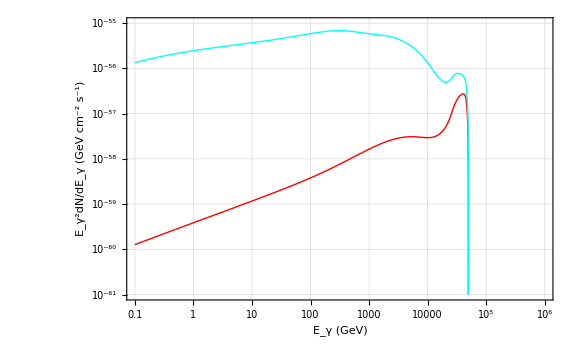

```mathematica
Module[{A,f1,f2,m1,envstyle,minE,maxE,expTicks},
A=2;
m1=81;
f1[x_]:=4/5. fVVqq[x]+1/5. fVVbb[x];
f2=fVVqq;
envstyle={(*Thick,*)Thickness[.01],Opacity[.3,Gray]};
minE=.75;
maxE=30;
expTicks=Table[{10^i,exponentForm[10^i]},{i,-8,-6}];
Show[pWDiffuseConstantBackground100000z23Redshift,pWDiffuseConstantBackground100000z46Redshift,
PlotStyle->{
envstyle,
envstyle,
{Thickness[.008],Blue}
},
Filling->{1->{2}},
FillingStyle->{Opacity[.2,Yellow]},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
ImageSize->Large, (* or Large*)
Epilog->{
Text[Rotate[Style["m_χ→ WW",20,Gray],0Degree],ImageScaled@{.65,.25}],
Text[Rotate[Style["m_χ = 100 TeV",20,Gray],0Degree],ImageScaled@{.65,.15}]
(*Text[Rotate[Style["bb",19,Blue],0Degree],ImageScaled@{.27,.92}],
Text[Rotate[Style["m_χ=40 GeV",17,Blue],0Degree],ImageScaled@{.27,.78}],
Text[Rotate[Style["VV (V→qq)",19,Red],0Degree],ImageScaled@{.83,.84}],
Text[Rotate[Style["m_χ=81, m_V=21 GeV",17,Red],0Degree],ImageScaled@{.82,.76}],
Text[Rotate[Style["3φ (φ→bb)",19,Darker[Green]],0Degree],ImageScaled@{.5,.55}],
Text[Rotate[Style["m_χ=123, m_φ=27 GeV",17,Darker[Green]],0Degree],ImageScaled@{.5,.45}],
Text[Style["a=2",19,Gray],ImageScaled@{.2,.23}]*)
}
(*PlotLegends->Placed[LineLegend[Range[1,6],LegendLayout->{"Row",2}],{.35,.25}]*)
(*PlotTheme->"Detailed"*)
]]
```

## Diffuse Gamma-Ray Background Dependence on Redshift